## The RGB Cube corners.

```mathematica
<<ToMatlab`
```

```mathematica
Clear[θ]
```

```mathematica
MatrixForm[TrigFactor[YABCube[θ]]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | ((-1)^(1/3) ((-1+(-1)^(1/3)) Cos[θ]+(ⅈ+(-1)^(5/6)) Sin[θ]))/(√6) | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | ((-1)^(5/6) (-ⅈ+(-1)^(1/6)) ((ⅈ+(-1)^(1/6)) Cos[θ]-(-1)^(1/3) Sin[θ]))/(√6) | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

```mathematica
cubeCorners[minMax_]:={{minMax[[1,1]],minMax[[1,2]],minMax[[1,2]],minMax[[1,1]],minMax[[1,1]],minMax[[1,1]],minMax[[1,2]],minMax[[1,2]]},{minMax[[2,1]],minMax[[2,1]],minMax[[2,2]],minMax[[2,2]],minMax[[2,2]],minMax[[2,1]],minMax[[2,1]],minMax[[2,2]]},{minMax[[3,1]],minMax[[3,1]],minMax[[3,1]],minMax[[3,1]],minMax[[3,2]],minMax[[3,2]],minMax[[3,2]],minMax[[3,2]]}};
```

```mathematica
YABCube[θ_] := cubeCorners[YABAxisRanges[θ]];
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
```

```mathematica
RGBAxisRanges = {{0,1},{0,1},{0,1}};
RGBCube = cubeCorners[RGBAxisRanges];
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
```

```mathematica
MatrixForm[YABCube[θ]]
```

(0 | √3 | √3 | 0 | 0 | 0 | √3 | √3
-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | -Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6) | -Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | -Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6)
-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | -Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | -Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | -Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6))

```mathematica
MatrixForm[RGBCube]
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
Map[Max,faces]
```

{4,8,7,8,8,6}

```mathematica
RGBCube3D[corners_]:=Module[{RGBCube,faces,ranges},
ranges =Transpose[{ Map[Min,corners],Map[Max,corners]}];Graphics3D[{Polygon[corners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[1]]]]]]],Polygon[corners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[2]]]]]]],Polygon[corners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[3]]]]]]],Polygon[corners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[4]]]]]]],Polygon[corners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[5]]]]]]],Polygon[corners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[6]]]]]]]},Lighting->"Neutral",PlotRange->{{ranges[[1,1]],ranges[[1,2]]},{ranges[[2,1]],ranges[[2,2]]},{ranges[[3,1]],ranges[[3,2]]}},Axes->True]
]
```

```mathematica
YABCube3D[θ_]:=Module[{corners,RGBCube,faces,ranges},corners = Transpose[YABCube[θ]];RGBCube = {{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}};
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
ranges = YABAxisRanges[θ];Graphics3D[{Polygon[corners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[1]]]]]]],Polygon[corners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[2]]]]]]],Polygon[corners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[3]]]]]]],Polygon[corners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[4]]]]]]],Polygon[corners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[5]]]]]]],Polygon[corners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[6]]]]]]]},Lighting->"Neutral",PlotRange->{{ranges[[1,1]],ranges[[1,2]]},{ranges[[2,1]],ranges[[2,2]]},{ranges[[3,1]],ranges[[3,2]]}},Axes->True]
]
```

```mathematica
Transpose[cubeCorners[ YABAxisRanges[θ]]]
```

{{0,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{√3,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{√3,-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{0,-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{0,-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)},{0,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)},{√3,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)},{√3,1,-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)}}

```mathematica
iYAB[θ]. YABCubeCorners
```

```mathematica
YABCube3D[θ_]:=Module[{RGBinYABcorners,RGBCubeCorners,YABCubeCorners,YABinRGBCubeCorners,faces,ranges},
RGBinYABcorners = Transpose[YABCube[θ]];
RGBCubeCorners = Transpose[cubeCorners[{{0,1},{0,1},{0,1}}]];YABCubeCorners =Transpose[cubeCorners[ YABAxisRanges[θ]]];
YABinRGBCubeCorners =Transpose[cubeCorners[ iYAB[θ]. cubeCorners[ YABAxisRanges[θ]]]];
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
ranges = YABAxisRanges[θ];Graphics3D[{Opacity[0.9],
Polygon[RGBinYABcorners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[1]]]]]]],Polygon[RGBinYABcorners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[2]]]]]]],Polygon[RGBinYABcorners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[3]]]]]]],Polygon[RGBinYABcorners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[4]]]]]]],Polygon[RGBinYABcorners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[5]]]]]]],Polygon[RGBinYABcorners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[6]]]]]]],
Opacity[0.2],
Polygon[YABCubeCorners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[1]]]]]]],Polygon[YABCubeCorners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[2]]]]]]],Polygon[YABCubeCorners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[3]]]]]]],Polygon[YABCubeCorners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[4]]]]]]],Polygon[YABCubeCorners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[5]]]]]]],Polygon[YABCubeCorners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[6]]]]]]]},Lighting->"Neutral",PlotRange->YABAxisRanges[θ],Axes->True]
]
```

## Rotation Matrices

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R=Function[{α,β, γ},Evaluate[TrigFactor[RotationMatrixX[α].RotationMatrixZ[γ].RotationMatrixY[β]]]];
MatrixForm[R[α,β, γ]]
```

(Cos[β] Cos[γ] | Sin[γ] | -Cos[γ] Sin[β]
1/4 (2 Cos[α-β]-2 Cos[α+β]+Sin[α-β-γ]+Sin[α+β-γ]-Sin[α-β+γ]-Sin[α+β+γ]) | Cos[α] Cos[γ] | 1/4 (-Cos[α-β-γ]+Cos[α+β-γ]+Cos[α-β+γ]-Cos[α+β+γ]+2 Sin[α-β]+2 Sin[α+β])
1/4 (Cos[α-β-γ]+Cos[α+β-γ]-Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-β]+2 Sin[α+β]) | -Cos[γ] Sin[α] | 1/4 (2 Cos[α-β]+2 Cos[α+β]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ]))

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
YAB=Function[{θ},Evaluate[TrigFactor[RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]]];
iYAB=Function[{θ},Evaluate[TrigFactor[RotationMatrixY[Pi/4].RotationMatrixZ[-ArcTan[1/Sqrt[2]]].RotationMatrixX[-θ]]]];
YABCube=Function[{θ},Evaluate[TrigFactor[FullSimplify[TrigToExp[YAB[θ].RGBCube]]]]];
```

```mathematica
Print[MatrixForm[YAB[θ]].MatrixForm[RGBCube],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[YAB[θ]. RGBCube]]],1]]
Print[MatrixForm[iYAB[θ]].MatrixForm[YABCube[θ]],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[iYAB[θ]. YABCube[θ]]]],1]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

(1/(√3) | -√(2/3) Sin[π/6+θ] | -√(2/3) Cos[π/6+θ]
1/(√3) | √(2/3) Cos[θ] | -√(2/3) Sin[θ]
1/(√3) | -√(2/3) Sin[π/6-θ] | √(2/3) Cos[π/6-θ]).(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)=(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

The inverse of a rotation is equal to the transpose of the rotation matrix

```mathematica
TrigFactor[FullSimplify[TrigToExp[Inverse[YAB[θ]]]]] == Transpose[YAB[θ]]
```

True

```mathematica
Manipulate[Show[YABCube3D[θ],Graphics3D[{Opacity[0.5],ranges = YABAxisRanges[θ];Cuboid[0.9{{ranges[[1,1]],ranges[[2,1]],ranges[[3,1]]},{ranges[[1,2]],ranges[[2,2]],ranges[[3,2]]}}]}]],{θ,0,Pi}]
```

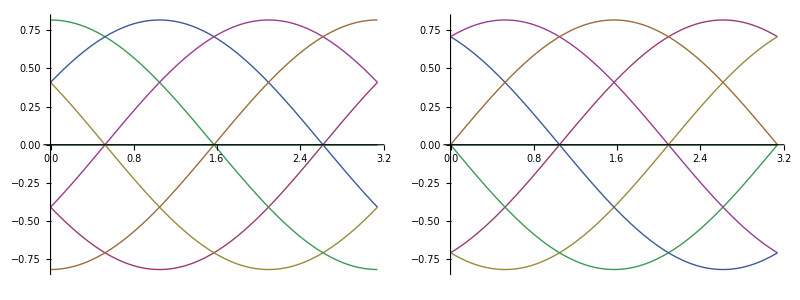

```mathematica
Grid[{{Plot[Evaluate[YABCube[θ][[2]]], {θ, 0, Pi}],Plot[Evaluate[YABCube[θ][[3]]], {θ, 0, Pi}]}}]
```

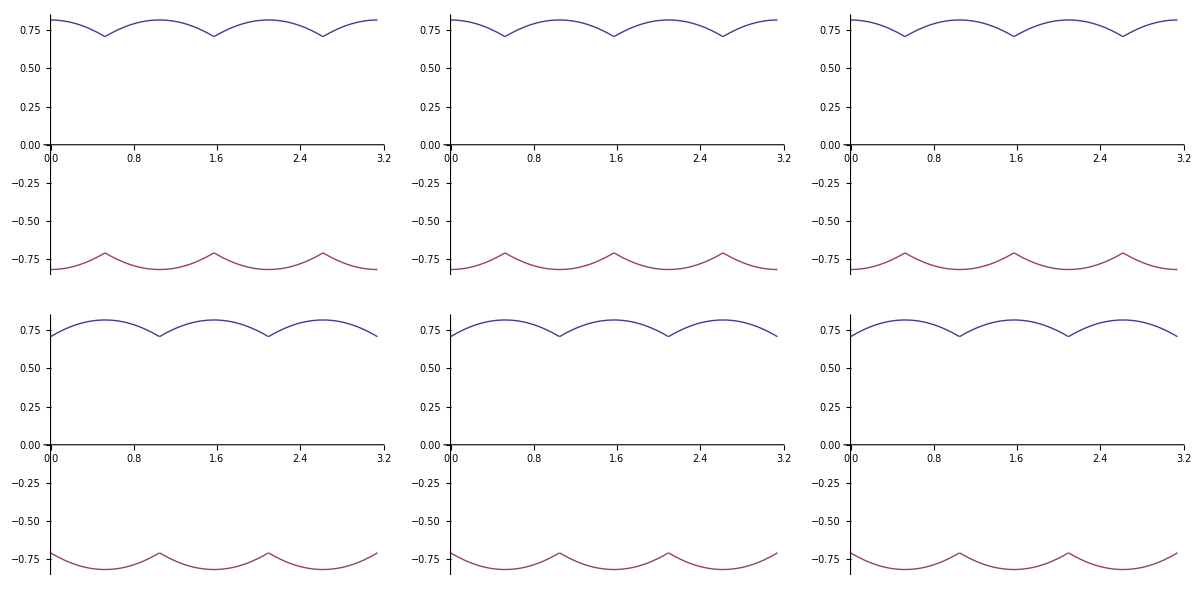

```mathematica
Grid[{{Plot[{Max[YABCube[θ ][[2]]],Min[YABCube[θ ][[2]]]},{θ,0,Pi}],Plot[{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{θ,0,Pi}],Plot[{√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]] ,-√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]]},{θ,0,Pi}]},{Plot[{Max[YABCube[θ ][[3]]],Min[YABCube[θ ][[3]]]},{θ,0,Pi}], Plot[{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)},{θ,0,Pi}],Plot[{√(2/3) Cos[π/6-Mod[θ,Pi/3]] ,-√(2/3) Cos[π/6-Mod[θ,Pi/3]]},{θ,0,Pi}]}}]
```

```mathematica
YABPolygon[θ_]:=Transpose[{Take[YABCube[θ ][[2]],{2,7}],Take[YABCube[θ ][[3]],{2,7}]}]
```

```mathematica
Manipulate[Graphics[{Black,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[YABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-√(2/3) ,√(2/3) },{-√(2/3) ,√(2/3) }}],{θ,0,Pi}]
```

```mathematica
YABAxisRanges[θ_]:={{0,Sqrt[3]},{-√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]] ,√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]]},{-√(2/3) Cos[π/6-Mod[θ,Pi/3]] ,√(2/3) Cos[π/6-Mod[θ,Pi/3]]}};
YABAxisLengths = Function[{θ},Evaluate[Flatten[YABAxisRanges[θ][[All,2]] - YABAxisRanges[θ][[All,1]]]]];
scaleVec = Function[{θ},Evaluate[Simplify[1/YABAxisLengths[θ]]]];
```

```mathematica
Print["L[θ] = ",MatrixForm[YABAxisLengths[θ]]," = ",MatrixForm[TrigExpand[YABAxisLengths[θ]]]," = ",MatrixForm[FullSimplify[TrigExpand[YABAxisLengths[θ]]]]]
Print["s[θ] = ",MatrixForm[scaleVec[θ]]," = ",MatrixForm[TrigExpand[scaleVec[θ]]]," = ",MatrixForm[FullSimplify[TrigExpand[scaleVec[θ]]]]]
```

L[θ] = (√3
2 √(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]
2 √(2/3) Cos[π/6-Mod[θ,π/3]]) = (√3
√2 Cos[Mod[-π/6+θ,π/3]]+√(2/3) Sin[Mod[-π/6+θ,π/3]]
√2 Cos[Mod[θ,π/3]]+√(2/3) Sin[Mod[θ,π/3]]) = (√3
√2 Cos[Mod[π/6+θ,π/3]]+√(2/3) Sin[Mod[π/6+θ,π/3]]
√2 Cos[Mod[θ,π/3]]+√(2/3) Sin[Mod[θ,π/3]])

s[θ] = (1/(√3)
1/2 √(3/2) Sec[1/6 (π-6 Mod[-π/6+θ,π/3])]
1/2 √(3/2) Sec[1/6 (π-6 Mod[θ,π/3])]) = (1/(√3)
(√6)/(2 √3 Cos[Mod[-π/6+θ,π/3]]+2 Sin[Mod[-π/6+θ,π/3]])
(√6)/(2 √3 Cos[Mod[θ,π/3]]+2 Sin[Mod[θ,π/3]])) = (1/(√3)
(√(3/2))/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])
(√(3/2))/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]))

```mathematica
scaleMatrix= Function[{θ},Evaluate[{{scaleVec[θ][[1]],0,0},{0,scaleVec[θ][[2]],0},{0,0,scaleVec[θ][[3]]}}]];
nYAB= Function[{θ},Evaluate[TrigReduce[FullSimplify[TrigExpand[scaleMatrix[θ]. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]]]]];
inYAB= Function[{θ},Evaluate[Inverse[nYAB[θ]]]];
MatrixForm[scaleMatrix[θ]]
MatrixForm[nYAB[θ]]
MatrixForm[TrigReduce[FullSimplify[TrigExpand[nYAB[θ]. RGBCube]]]]
```

(1/(√3) | 0 | 0
0 | 1/2 √(3/2) Sec[1/6 (π-6 Mod[-π/6+θ,π/3])] | 0
0 | 0 | 1/2 √(3/2) Sec[1/6 (π-6 Mod[θ,π/3])])

(1/3 | 1/3 | 1/3
(-Cos[θ]-√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | Cos[θ]/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]) | (-Cos[θ]+√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]))
(-√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | -Sin[θ]/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]) | (√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])))

(0 | 1/3 | 2/3 | 1/3 | 2/3 | 1/3 | 2/3 | 1
0 | (-Cos[θ]-√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | (Cos[θ]-√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | Cos[θ]/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]) | (Cos[θ]+√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | (-Cos[θ]+√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | -Cos[θ]/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]) | 0
0 | (-√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | (-√3 Cos[θ]-Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | -Sin[θ]/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]) | (√3 Cos[θ]-Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | (√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | Sin[θ]/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]) | 0)

```mathematica
Manipulate[MatrixForm[FullSimplify[nYAB[θ]. RGBCube]],{θ,0,Pi}]
```

```mathematica
nYABCube= Function[{θ},Evaluate[FullSimplify[nYAB[θ].RGBCube]]];
```

```mathematica
nYABPolygon= Function[{θ},Evaluate[Transpose[{Take[nYABCube[θ ][[2]],{2,7}],Take[nYABCube[θ ][[3]],{2,7}]}]]];
```

```mathematica
Manipulate[LxyAxisRanges = Simplify[YABAxisRanges[θ ]];Grid[{{Graphics[{Black,Rectangle[Sequence@@Transpose[{LxyAxisRanges[[2]],LxyAxisRanges[[3]]}]],Blue,Polygon[nYABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-1/2,1/2},{-1/2 ,1/2}}],MatrixForm[{Row[{" θ = ",θ}],Row[{LxyAxisRanges[[1,1]],"< L < ",LxyAxisRanges[[1,2]]}], Row[{LxyAxisRanges[[2,1]],"< x < ",LxyAxisRanges[[2,2]]}],Row[{LxyAxisRanges[[3,1]],"< y < ",LxyAxisRanges[[3,2]]}]}]}}],{θ,0,Pi}]
```

## Discrete Representation of the rotation

We have a source which makes discrete steps of 1/srcRange the question is to what degree of precision do we need to represent the transformation given that we require a precision of 1/wrkRange. What is required is the smallest number which can result from the transformation of a unit cube!

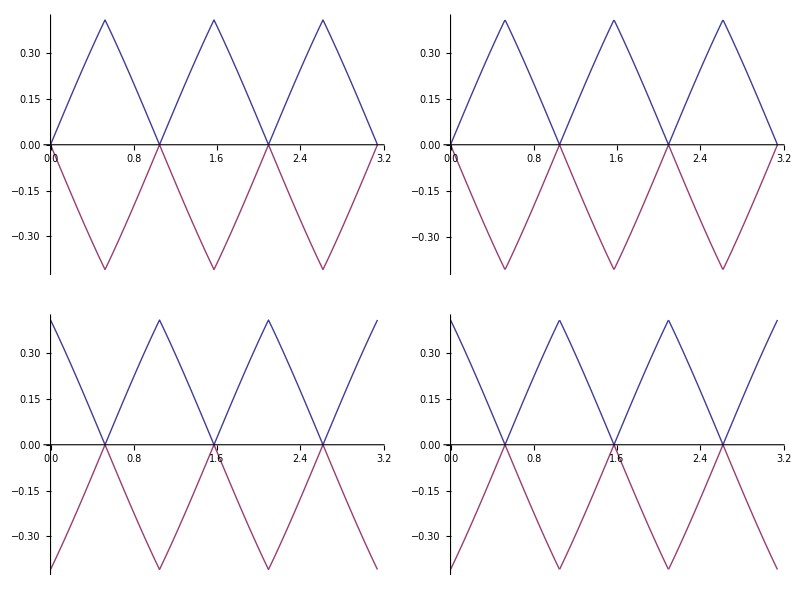

```mathematica
Grid[{{Plot[{Min[Abs[YABCube[θ ][[3,{2,3,4,5,6,7}]]]],-Min[Abs[YABCube[θ ][[3,{2,3,4,5,6,7}]]]]},{θ,0,Pi}], Plot[{√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]]},{θ,0,Pi}]},{Plot[{Min[Abs[YABCube[θ ][[2,{2,3,4,5,6,7}]]]],-Min[Abs[YABCube[θ ][[2,{2,3,4,5,6,7}]]]]},{θ,0,Pi}],Plot[{√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]]},{θ,0,Pi}]}}]
```

```mathematica
Manipulate[{MatrixForm[N[d[YAB[θ],srcRange]]- N[YAB[θ]]],MatrixForm[N[YAB[θ]]]},{θ,0,Pi},{srcRange,1,255,1}]
```

```mathematica
]
```

```mathematica
MatrixForm[YAB[θ].{1,1,1}]
```

(√3
0
0)

```mathematica
MatrixForm[Map[Solve[{#1==0,-Pi ≤θ ≤Pi},θ]&,YAB[θ],{2}]]
```

({} | {} | {}
{{θ→-π/6},{θ→(5 π)/6}} | {{θ→-π/2},{θ→π/2}} | {{θ→-(5 π)/6},{θ→π/6}}
{{θ→-(2 π)/3},{θ→π/3}} | {{θ→0},{θ→-π},{θ→π}} | {{θ→-π/3},{θ→(2 π)/3}})

```mathematica
maskPos[θ_]:=Evaluate[Map[Reduce[{#1>0,0 ≤θ <2Pi},θ]&,YAB[θ],{2}]]
maskNeg[θ_]:=Evaluate[Map[Reduce[{#1<0,0 ≤θ <2Pi},θ]&,YAB[θ],{2}]]
MatrixForm[maskPos[θ]]
MatrixForm[maskNeg[θ]]
```

(0≤θ<2 π | 0≤θ<2 π | 0≤θ<2 π
(5 π)/6<θ<(11 π)/6 | 0≤θ<π/2||(3 π)/2<θ<2 π | π/6<θ<(7 π)/6
π/3<θ<(4 π)/3 | π<θ<2 π | 0≤θ<(2 π)/3||(5 π)/3<θ<2 π)

(False | False | False
0≤θ<(5 π)/6||(11 π)/6<θ<2 π | π/2<θ<(3 π)/2 | 0≤θ<π/6||(7 π)/6<θ<2 π
0≤θ<π/3||(4 π)/3<θ<2 π | 0<θ<π | (2 π)/3<θ<(5 π)/3)

```mathematica
Manipulate[{MatrixForm[maskPos[θ]],MatrixForm[Sign[rYAB[θ]]],MatrixForm[Sign[Sign[rYAB[θ]].{1,1,1}]],MatrixForm[(Sign[Sign[rYAB[θ]].{1,1,1}] Sign[rYAB[θ]] +1)/2],θ},{θ,0,2 Pi,Pi/12}]
```

```mathematica
Manipulate[{MatrixForm[maskPos[θ]],MatrixForm[Sign[rYAB[θ]]],MatrixForm[Sign[Sign[rYAB[θ]].{1,1,1}]],MatrixForm[(Sign[Sign[rYAB[θ]].{1,1,1}] Sign[rYAB[θ]] +1)/2],MatrixForm[((Sign[Sign[rYAB[θ]].{1,1,1}] Sign[rYAB[θ]] +1)/2).{r,g,b}],StringJoin[" θ = ",ToString[θ,TraditionalForm ]],inPiBySixRegaion[θ]},{θ,Pi/12,2 Pi,Pi/6}]
```

```mathematica
MatrixForm[Table[{MatrixForm[((Sign[Sign[rYAB[θ]].{1,1,1}] Sign[rYAB[θ]] +1)/2).{r,g,b}],inPiBySixRegaion[θ]} ,{θ,Pi/12,Pi,Pi/6}]]
```

((b+g+r
b+r
g+r) | TraditionalForm`0 < θ < TraditionalForm`π/6
(b+g+r
b+g
g+r) | TraditionalForm`π/6 < θ < TraditionalForm`π/3
(b+g+r
b+g
b+r) | TraditionalForm`π/3 < θ < TraditionalForm`π/2
(b+g+r
g+r
b+r) | TraditionalForm`π/2 < θ < TraditionalForm`2\ π/3
(b+g+r
g+r
b+g) | TraditionalForm`2\ π/3 < θ < TraditionalForm`5\ π/6
(b+g+r
b+r
b+g) | TraditionalForm`5\ π/6 < θ < TraditionalForm`π)

```mathematica
MatrixForm[Table[mat = (((Sign[Sign[rYAB[θ]].{1,1,1}] Sign[rYAB[θ]] +1)/2).{r,g,b});{MatrixForm[mat],mat[[2]]<1 && mat[[3]]<1,inPiBySixRegaion[θ]} ,{θ,Pi/12 -Pi,Pi,Pi/6}]]
```

((b+g+r
b+r
g+r) | b+r<1&&g+r<1 | TraditionalForm`-π < θ < TraditionalForm`-5\ π/6
(b+g+r
b+g
g+r) | b+g<1&&g+r<1 | TraditionalForm`-5\ π/6 < θ < TraditionalForm`-2\ π/3
(b+g+r
b+g
b+r) | b+g<1&&b+r<1 | TraditionalForm`-2\ π/3 < θ < TraditionalForm`-π/2
(b+g+r
g+r
b+r) | g+r<1&&b+r<1 | TraditionalForm`-π/2 < θ < TraditionalForm`-π/3
(b+g+r
g+r
b+g) | g+r<1&&b+g<1 | TraditionalForm`-π/3 < θ < TraditionalForm`-π/6
(b+g+r
b+r
b+g) | b+r<1&&b+g<1 | TraditionalForm`-π/6 < θ < TraditionalForm`0
(b+g+r
b+r
g+r) | b+r<1&&g+r<1 | TraditionalForm`0 < θ < TraditionalForm`π/6
(b+g+r
b+g
g+r) | b+g<1&&g+r<1 | TraditionalForm`π/6 < θ < TraditionalForm`π/3
(b+g+r
b+g
b+r) | b+g<1&&b+r<1 | TraditionalForm`π/3 < θ < TraditionalForm`π/2
(b+g+r
g+r
b+r) | g+r<1&&b+r<1 | TraditionalForm`π/2 < θ < TraditionalForm`2\ π/3
(b+g+r
g+r
b+g) | g+r<1&&b+g<1 | TraditionalForm`2\ π/3 < θ < TraditionalForm`5\ π/6
(b+g+r
b+r
b+g) | b+r<1&&b+g<1 | TraditionalForm`5\ π/6 < θ < TraditionalForm`π)

```mathematica
Clear[cyclicSolve]
cyclicSolve[cond_,n_]:=Module[{hCond},hCond = HoldComplete[cond][[1,0]][HoldComplete[cond][[1,1]]+ n*Pi,HoldComplete[cond][[1,2]],HoldComplete[cond][[1,3]]+ n*Pi];ReleaseHold[hCond]/.Flatten[FindInstance[ReleaseHold[hCond]&&n∈Integers,n]/.List[]->List[Rule[n,0]] ]]

SetAttributes[cyclicSolve,HoldAllComplete]
```

```mathematica
inPiBySixRegion[θ_,ψ_]:=StringJoin[ToString[Floor[6 θ/Pi]Pi/6,TraditionalForm]," < ",ToString[ψ,TraditionalForm]," < ",ToString[(Floor[6 θ/Pi]+1)Pi/6,TraditionalForm ]]
```

```mathematica
Clear[YABSameSign];
YABSameSign =Function[{θ},Evaluate[Piecewise[Table[ {((Sign[Sign[rYAB[ϕ]].{1,1,1}] Sign[rYAB[ϕ]] +1)/2),cSol[ToExpression[inPiBySixRegion[ϕ,θ]],n]},{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
Clear[YABDiscretFactor];
YABDiscretFactor =Function[{θ,wrkRange,ψ},Evaluate[Piecewise[Table[{(  {1/3,2/wrkRange,2/wrkRange}  YABSameSign[ϕ] Map[If[#≥1/2,1,0]&,Abs[rYAB[ϕ]],{2}] rYAB[θ]).{1,1,1},cSol[ToExpression[inPiBySixRegion[ϕ,ψ]],n]} ,{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
Clear[fYAB,ϕ,ψ]
fYAB =Function[{θ,wrkRange,ψ},Evaluate[Piecewise[Table[ {{1,wrkRange,wrkRange} rYAB[θ]/YABDiscretFactor[θ,1,ϕ],cSol[ToExpression[inPiBySixRegion[ϕ,ψ]],n]},{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
YABDiscretFactor[θ,1,Pi/12]
```

{1,-2 Sin[π/6+θ],-2 Cos[π/6+θ]}

```mathematica
mat = fYAB[θ,1,θ];
factor=YABDiscretFactor[θ,rRange,θ];
i=2;
TableForm[Table[{MatrixForm[factor[[1,i,1]]]⊗ int[MatrixForm[{1,rRange,rRange}] ⊗ MatrixForm[mat[[1,i,1]]]],mat[[1,i,2,1]]},{i,1,6}]]
```

(1
-(2 Sin[π/6+θ])/rRange
-(2 Cos[π/6+θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 | -1/2 Cos[θ] Csc[π/6+θ] | 1/2 Csc[π/6+θ] Sin[π/6-θ]
1/2 | 1/2 Sec[π/6+θ] Sin[θ] | -1/2 Cos[π/6-θ] Sec[π/6+θ])] | n π<θ<π/6+n π
(1
(2 Cos[θ])/rRange
-(2 Sin[θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
-1/2 Sec[θ] Sin[π/6+θ] | 1/2 | -1/2 Sec[θ] Sin[π/6-θ]
1/2 Cos[π/6+θ] Csc[θ] | 1/2 | -1/2 Cos[π/6-θ] Csc[θ])] | π/6+n π<θ<π/3+n π
(1
-(2 Sin[π/6-θ])/rRange
(2 Cos[π/6-θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 Csc[π/6-θ] Sin[π/6+θ] | -1/2 Cos[θ] Csc[π/6-θ] | 1/2
-1/2 Cos[π/6+θ] Sec[π/6-θ] | -1/2 Sec[π/6-θ] Sin[θ] | 1/2)] | π/3+n π<θ<π/2+n π
(1
-(2 Sin[π/6+θ])/rRange
-(2 Cos[π/6+θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 | -1/2 Cos[θ] Csc[π/6+θ] | 1/2 Csc[π/6+θ] Sin[π/6-θ]
1/2 | 1/2 Sec[π/6+θ] Sin[θ] | -1/2 Cos[π/6-θ] Sec[π/6+θ])] | π/2+n π<θ<(2 π)/3+n π
(1
(2 Cos[θ])/rRange
-(2 Sin[θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
-1/2 Sec[θ] Sin[π/6+θ] | 1/2 | -1/2 Sec[θ] Sin[π/6-θ]
1/2 Cos[π/6+θ] Csc[θ] | 1/2 | -1/2 Cos[π/6-θ] Csc[θ])] | (2 π)/3+n π<θ<(5 π)/6+n π
(1
-(2 Sin[π/6-θ])/rRange
(2 Cos[π/6-θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 Csc[π/6-θ] Sin[π/6+θ] | -1/2 Cos[θ] Csc[π/6-θ] | 1/2
-1/2 Cos[π/6+θ] Sec[π/6-θ] | -1/2 Sec[π/6-θ] Sin[θ] | 1/2)] | (5 π)/6+n π<θ<π+n π

```mathematica
mat = fYAB[θ,1,θ];
factor=YABDiscretFactor[θ,rRange,θ];
i=2;
TableForm[Table[{MatrixForm[factor[[1,i,1]]]⊗ int[MatrixForm[{1,rRange,rRange}] ⊗ MatrixForm[mat[[1,i,1]]]],mat[[1,i,2,1]]},{i,1,6}]]
```

(1
-(2 Sin[π/6+θ])/rRange
-(2 Cos[π/6+θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 | -1/2 Cos[θ] Csc[π/6+θ] | 1/2 Csc[π/6+θ] Sin[π/6-θ]
1/2 | 1/2 Sec[π/6+θ] Sin[θ] | -1/2 Cos[π/6-θ] Sec[π/6+θ])] | n π<θ<π/6+n π
(1
(2 Cos[θ])/rRange
-(2 Sin[θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
-1/2 Sec[θ] Sin[π/6+θ] | 1/2 | -1/2 Sec[θ] Sin[π/6-θ]
1/2 Cos[π/6+θ] Csc[θ] | 1/2 | -1/2 Cos[π/6-θ] Csc[θ])] | π/6+n π<θ<π/3+n π
(1
-(2 Sin[π/6-θ])/rRange
(2 Cos[π/6-θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 Csc[π/6-θ] Sin[π/6+θ] | -1/2 Cos[θ] Csc[π/6-θ] | 1/2
-1/2 Cos[π/6+θ] Sec[π/6-θ] | -1/2 Sec[π/6-θ] Sin[θ] | 1/2)] | π/3+n π<θ<π/2+n π
(1
-(2 Sin[π/6+θ])/rRange
-(2 Cos[π/6+θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 | -1/2 Cos[θ] Csc[π/6+θ] | 1/2 Csc[π/6+θ] Sin[π/6-θ]
1/2 | 1/2 Sec[π/6+θ] Sin[θ] | -1/2 Cos[π/6-θ] Sec[π/6+θ])] | π/2+n π<θ<(2 π)/3+n π
(1
(2 Cos[θ])/rRange
-(2 Sin[θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
-1/2 Sec[θ] Sin[π/6+θ] | 1/2 | -1/2 Sec[θ] Sin[π/6-θ]
1/2 Cos[π/6+θ] Csc[θ] | 1/2 | -1/2 Cos[π/6-θ] Csc[θ])] | (2 π)/3+n π<θ<(5 π)/6+n π
(1
-(2 Sin[π/6-θ])/rRange
(2 Cos[π/6-θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1/2 Csc[π/6-θ] Sin[π/6+θ] | -1/2 Cos[θ] Csc[π/6-θ] | 1/2
-1/2 Cos[π/6+θ] Sec[π/6-θ] | -1/2 Sec[π/6-θ] Sin[θ] | 1/2)] | (5 π)/6+n π<θ<π+n π

```mathematica
Flatten[fYAB[θ,1,Pi/12][[{2,3}]]]
```

{1/2,-1/2 Cos[θ] Csc[π/6+θ],1/2 Csc[π/6+θ] Sin[π/6-θ],1/2,1/2 Sec[π/6+θ] Sin[θ],-1/2 Cos[π/6-θ] Sec[π/6+θ]}

```mathematica
Definition[fYAB]
```

fYAB=Function[{θ,wrkRange,ψ},Piecewise[{{{{1,1,1},{wrkRange/2,-1/2 wrkRange Cos[θ] Csc[π/6+θ],1/2 wrkRange Csc[π/6+θ] Sin[π/6-θ]},{wrkRange/2,1/2 wrkRange Sec[π/6+θ] Sin[θ],-1/2 wrkRange Cos[π/6-θ] Sec[π/6+θ]}}, cyclicSolve[0<ψ<π/6,n]}, {{{1,1,1},{-1/2 wrkRange Sec[θ] Sin[π/6+θ],wrkRange/2,-1/2 wrkRange Sec[θ] Sin[π/6-θ]},{1/2 wrkRange Cos[π/6+θ] Csc[θ],wrkRange/2,-1/2 wrkRange Cos[π/6-θ] Csc[θ]}}, cyclicSolve[π/6<ψ<π/3,n]}, {{{1,1,1},{1/2 wrkRange Csc[π/6-θ] Sin[π/6+θ],-1/2 wrkRange Cos[θ] Csc[π/6-θ],wrkRange/2},{-1/2 wrkRange Cos[π/6+θ] Sec[π/6-θ],-1/2 wrkRange Sec[π/6-θ] Sin[θ],wrkRange/2}}, cyclicSolve[π/3<ψ<π/2,n]}, {{{1,1,1},{wrkRange/2,-1/2 wrkRange Cos[θ] Csc[π/6+θ],1/2 wrkRange Csc[π/6+θ] Sin[π/6-θ]},{wrkRange/2,1/2 wrkRange Sec[π/6+θ] Sin[θ],-1/2 wrkRange Cos[π/6-θ] Sec[π/6+θ]}}, cyclicSolve[π/2<ψ<(2 π)/3,n]}, {{{1,1,1},{-1/2 wrkRange Sec[θ] Sin[π/6+θ],wrkRange/2,-1/2 wrkRange Sec[θ] Sin[π/6-θ]},{1/2 wrkRange Cos[π/6+θ] Csc[θ],wrkRange/2,-1/2 wrkRange Cos[π/6-θ] Csc[θ]}}, cyclicSolve[(2 π)/3<ψ<(5 π)/6,n]}, {{{1,1,1},{1/2 wrkRange Csc[π/6-θ] Sin[π/6+θ],-1/2 wrkRange Cos[θ] Csc[π/6-θ],wrkRange/2},{-1/2 wrkRange Cos[π/6+θ] Sec[π/6-θ],-1/2 wrkRange Sec[π/6-θ] Sin[θ],wrkRange/2}}, cyclicSolve[(5 π)/6<ψ<π,n]}, {Null, True}}]]

```mathematica
Clear[n]
```

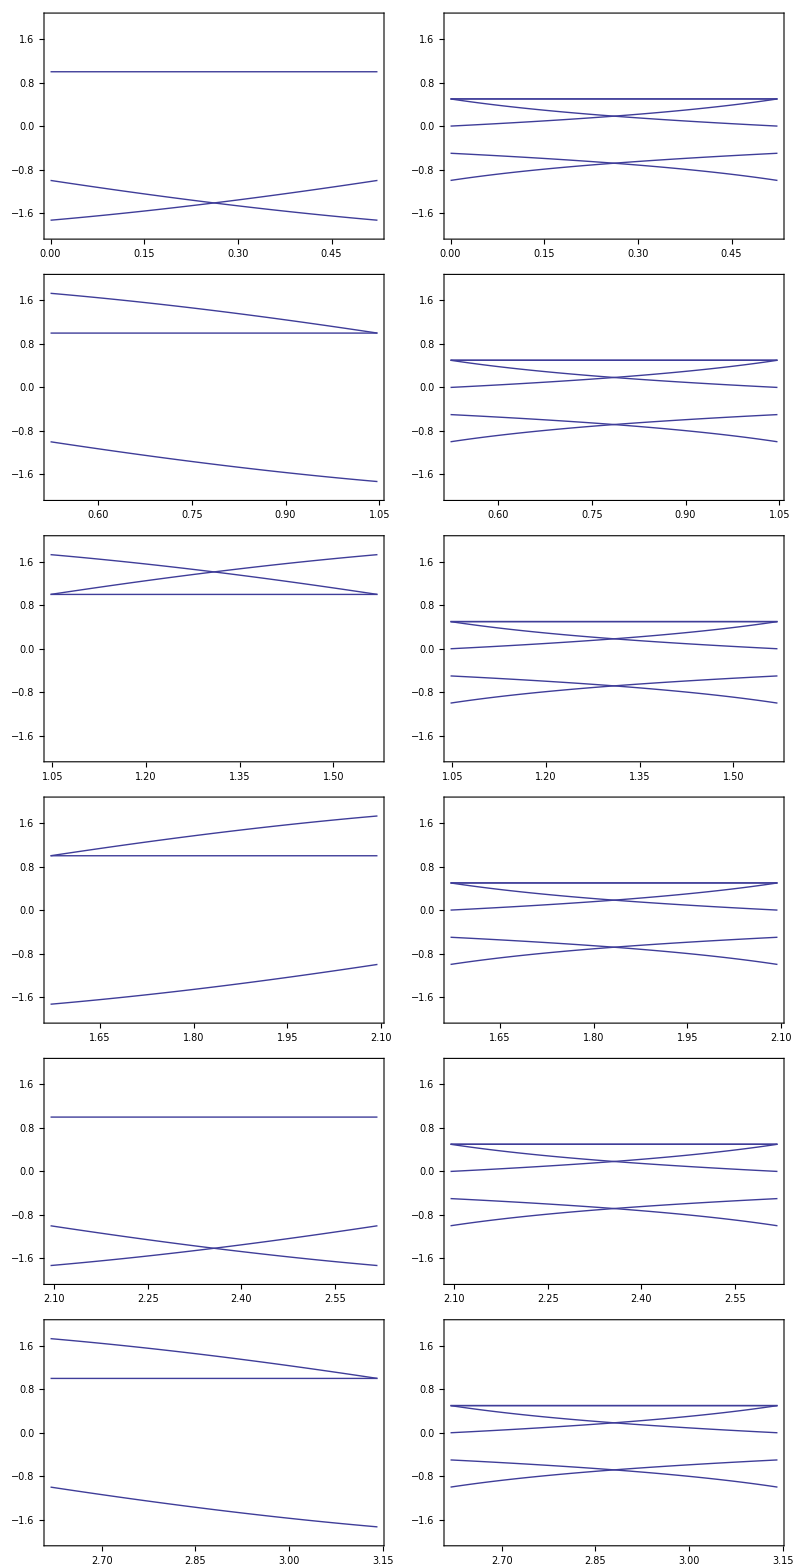

```mathematica
Grid[Table[{Plot[Flatten[YABDiscretFactor[θ,1,m Pi/12]],{θ,(m-1)  Pi/12,(m+1) Pi/12},PlotRange->{All,{-2,2}},Frame -> True],Plot[Flatten[fYAB[θ,1,m Pi/12][[{2,3}]]],{θ,(m-1)  Pi/12,(m+1) Pi/12},PlotRange->{All,{-2,2}},Frame -> True]},{m,1,12,2}]]
```

```mathematica
Flatten[fYAB[θ,1,Pi/12][[{2,3}]]]
```

```mathematica
Plot[Flatten[fYAB[θ,1,Pi/12][[{2,3}]]],{θ,0, Pi}]
```

-Graphics-

```mathematica
RGBCube
```

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
mForm[mat_]:=ToString[MatrixForm[mat],TraditionalForm];
Clear[n,factor,mat,error,pts,iRot,rot,ptsError];
Manipulate[
factor =YABDiscretFactor[θ,2^n,θ];
mat =  IntegerPart[fYAB[θ,2^n,θ]];
error = factor  mat- N[rYAB[θ]];
pts =2^n  RGBCube;
iRot = mat . pts;
rot = rYAB[θ] . pts;
ptsError = factor iRot - rot;
{StringJoin[mForm[factor] ,"⊗", mForm[ mat]," - ",mForm[rYAB[θ]]," = ",mForm[error]],MatrixForm[ptsError]},{θ,0,Pi},{n,1,32,1}]
```

```mathematica
factor[θ_,n_] :=YABDiscretFactor[θ,2^n,θ];
mat[θ_,n_] :=IntegerPart[fYAB[θ,2^n,θ]];
error[θ_,n_] :=YABDiscretFactor[θ,2^n,θ]  IntegerPart[fYAB[θ,2^n,θ]]- rYAB[θ];
pts =val  RGBCube;
iRot[θ_,n_,val_] :=val IntegerPart[fYAB[θ,2^n,θ]] . RGBCube;
rot[θ_] :=rYAB[θ] . pts;
YABError[θ_,n_] := factor[θ,n]IntegerPart[fYAB[θ,2^n,θ]] . RGBCube- rYAB[θ] . RGBCube;
```

```mathematica
Clear[fYABError,n,m]
fYABError =Function[{θ,m,ψ,p,pp},Evaluate[Piecewise[Table[ {Part[Assuming[Element[m,Integers]&& m≥1,Simplify[2^m (YABDiscretFactor[θ,2^m,ϕ]IntegerPart[fYAB[θ,2^m,ϕ]] - rYAB[θ] )]],p,pp],cSol[ToExpression[inPiBySixRegion[ϕ,ψ]],n]},{ϕ,Pi/12 ,Pi,Pi/6}],Null]/. cSol->cyclicSolve]];
```

```mathematica
Clear[fYABError,n,m]
fYABError =Function[{θ,m,ψ,p,pp},Evaluate[Piecewise[Table[ {Part[Assuming[Element[m,Integers]&& m≥1,Simplify[2^m (YABDiscretFactor[θ,2^m,ϕ]IntegerPart[fYAB[θ,2^m,ϕ]] - rYAB[θ] )]],p,pp],cSol[ToExpression[inPiBySixRegion[ϕ,ψ]],n]},{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
Clear[fYABError,n,m]
fYABError =Function[{θ,m,ψ,p,pp},Evaluate[Piecewise[Table[ {Part[Assuming[Element[m,Integers]&& m≥1,Simplify[2^m (YABDiscretFactor[θ,2^m,ϕ]IntegerPart[fYAB[θ,2^m,ϕ]] - rYAB[θ] )]],p,pp],ToExpression[inPiBySixRegion[ϕ,ψ]]},{ϕ,Pi/12 ,Pi,Pi/6}],Null]]];
```

```mathematica
fYABError[θ,m,ψ,Sequence[2,2]]
```

Piecewise[{{-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ], 0<ψ<π/6}, {0, π/6<ψ<π/3}, {-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ], π/3<ψ<π/2}, {-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ], π/2<ψ<(2 π)/3}, {0, (2 π)/3<ψ<(5 π)/6}, {-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ], (5 π)/6<ψ<π}, {Null, True}}]

```mathematica
fYABError
```

Function[{θ,m,ψ,p,pp},Piecewise[{{{{0,0,0},{0,-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^m Sin[π/6-θ]-2 IntegerPart[2^(-1+m) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]},{0,-2 Cos[π/6+θ] IntegerPart[2^(-1+m) Sec[π/6+θ] Sin[θ]]+2^m Sin[θ],-2^m Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+m) Cos[π/6-θ] Sec[π/6+θ]]}}⟦p,pp⟧, 0<ψ<π/6}, {{{0,0,0},{-2 Cos[θ] IntegerPart[2^(-1+m) Sec[θ] Sin[π/6+θ]]+2^m Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[2^(-1+m) Sec[θ] Sin[π/6-θ]]+2^m Sin[π/6-θ]},{2^m Cos[π/6+θ]-2 IntegerPart[2^(-1+m) Cos[π/6+θ] Csc[θ]] Sin[θ],0,-2^m Cos[π/6-θ]+2 IntegerPart[2^(-2+m) (1+√3 Cot[θ])] Sin[θ]}}⟦p,pp⟧, π/6<ψ<π/3}, {{{0,0,0},{-2 IntegerPart[2^(-1+m) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+2^m Sin[π/6+θ],-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0},{2^m Cos[π/6+θ]-2 Cos[π/6-θ] IntegerPart[2^(-1+m) Cos[π/6+θ] Sec[π/6-θ]],-2 Cos[π/6-θ] IntegerPart[(2^m Sin[θ])/(√3 Cos[θ]+Sin[θ])]+2^m Sin[θ],0}}⟦p,pp⟧, π/3<ψ<π/2}, {{{0,0,0},{0,-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^m Sin[π/6-θ]-2 IntegerPart[2^(-1+m) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]},{0,-2 Cos[π/6+θ] IntegerPart[2^(-1+m) Sec[π/6+θ] Sin[θ]]+2^m Sin[θ],-2^m Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+m) Cos[π/6-θ] Sec[π/6+θ]]}}⟦p,pp⟧, π/2<ψ<(2 π)/3}, {{{0,0,0},{-2 Cos[θ] IntegerPart[2^(-1+m) Sec[θ] Sin[π/6+θ]]+2^m Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[2^(-1+m) Sec[θ] Sin[π/6-θ]]+2^m Sin[π/6-θ]},{2^m Cos[π/6+θ]-2 IntegerPart[2^(-1+m) Cos[π/6+θ] Csc[θ]] Sin[θ],0,-2^m Cos[π/6-θ]+2 IntegerPart[2^(-2+m) (1+√3 Cot[θ])] Sin[θ]}}⟦p,pp⟧, (2 π)/3<ψ<(5 π)/6}, {{{0,0,0},{-2 IntegerPart[2^(-1+m) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+2^m Sin[π/6+θ],-2^m Cos[θ]+2 IntegerPart[2^(-1+m) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0},{2^m Cos[π/6+θ]-2 Cos[π/6-θ] IntegerPart[2^(-1+m) Cos[π/6+θ] Sec[π/6-θ]],-2 Cos[π/6-θ] IntegerPart[(2^m Sin[θ])/(√3 Cos[θ]+Sin[θ])]+2^m Sin[θ],0}}⟦p,pp⟧, (5 π)/6<ψ<π}, {Null, True}}]]

```mathematica
fYABError[θ,8,Pi/12,2,2]
```

-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6+θ]] Sin[π/6+θ]

```mathematica
Union[Flatten[fYABError[θ,8,Pi/12]]]
```

{0,-256 Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[128 Cos[π/6-θ] Sec[π/6+θ]],-2 Cos[π/6+θ] IntegerPart[128 Sec[π/6+θ] Sin[θ]]+256 Sin[θ],-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],256 Sin[π/6-θ]-2 IntegerPart[128 Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]}

```mathematica
fYABError[θ,8,θ,2,All]
```

Piecewise[{{{0,-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],256 Sin[π/6-θ]-2 IntegerPart[128 Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]}, 0<θ<π/6}, {{-2 Cos[θ] IntegerPart[128 Sec[θ] Sin[π/6+θ]]+256 Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[128 Sec[θ] Sin[π/6-θ]]+256 Sin[π/6-θ]}, π/6<θ<π/3}, {{-2 IntegerPart[128 Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+256 Sin[π/6+θ],-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0}, π/3<θ<π/2}, {{0,-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],256 Sin[π/6-θ]-2 IntegerPart[128 Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]}, π/2<θ<(2 π)/3}, {{-2 Cos[θ] IntegerPart[128 Sec[θ] Sin[π/6+θ]]+256 Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[128 Sec[θ] Sin[π/6-θ]]+256 Sin[π/6-θ]}, (2 π)/3<θ<(5 π)/6}, {{-2 IntegerPart[128 Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+256 Sin[π/6+θ],-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0}, (5 π)/6<θ<π}, {Null, True}}]

```mathematica
PiecewiseExpand[fYABError[θ,8,θ,2,All]]
```

Piecewise[{{Null, θ==π/6||θ==π/3||θ==π/2||θ==(2 π)/3||θ==(5 π)/6||θ≥π||θ≤0}, {{0,-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],256 Sin[π/6-θ]-2 IntegerPart[128 Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]}, 0<θ<π/6||π/2<θ<(2 π)/3}, {{-2 Cos[θ] IntegerPart[128 Sec[θ] Sin[π/6+θ]]+256 Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[128 Sec[θ] Sin[π/6-θ]]+256 Sin[π/6-θ]}, π/6<θ<π/3||(2 π)/3<θ<(5 π)/6}, {{-2 IntegerPart[128 Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+256 Sin[π/6+θ],-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0}, True}}]

```mathematica
PiecewiseExpand[Assuming[0<=θ≤Pi,Simplify[fYABError[θ,8,θ,2,All]]]]
```

Piecewise[{{{0,-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],256 Sin[π/6-θ]-2 IntegerPart[128 Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]}, (n π<θ<(1/6+n) π/.FindInstance[n π<θ<(1/6+n) π&&n∈Integers,n])||(!((1/6+n) π<θ<(1/3+n) π/.FindInstance[(1/6+n) π<θ<(1/3+n) π&&n∈Integers,n])&&!((1/3+n) π<θ<(1/2+n) π/.FindInstance[(1/3+n) π<θ<(1/2+n) π&&n∈Integers,n])&&((1/2+n) π<θ<(2/3+n) π/.FindInstance[(1/2+n) π<θ<(2/3+n) π&&n∈Integers,n]))}, {{-2 Cos[θ] IntegerPart[64+64 √3 Tan[θ]]+256 Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[64-64 √3 Tan[θ]]+256 Sin[π/6-θ]}, ((1/6+n) π<θ<(1/3+n) π/.FindInstance[(1/6+n) π<θ<(1/3+n) π&&n∈Integers,n])||(!((1/3+n) π<θ<(1/2+n) π/.FindInstance[(1/3+n) π<θ<(1/2+n) π&&n∈Integers,n])&&!((1/2+n) π<θ<(2/3+n) π/.FindInstance[(1/2+n) π<θ<(2/3+n) π&&n∈Integers,n])&&((2/3+n) π<θ<(5/6+n) π/.FindInstance[(2/3+n) π<θ<(5/6+n) π&&n∈Integers,n]))}, {{-2 IntegerPart[128 Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+256 Sin[π/6+θ],-256 Cos[θ]+2 IntegerPart[128 Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0}, ((1/3+n) π<θ<(1/2+n) π/.FindInstance[(1/3+n) π<θ<(1/2+n) π&&n∈Integers,n])||(!((1/2+n) π<θ<(2/3+n) π/.FindInstance[(1/2+n) π<θ<(2/3+n) π&&n∈Integers,n])&&!((2/3+n) π<θ<(5/6+n) π/.FindInstance[(2/3+n) π<θ<(5/6+n) π&&n∈Integers,n])&&((5/6+n) π<θ<(1+n) π/.FindInstance[(5/6+n) π<θ<(1+n) π&&n∈Integers,n]))}, {Null, True}}]

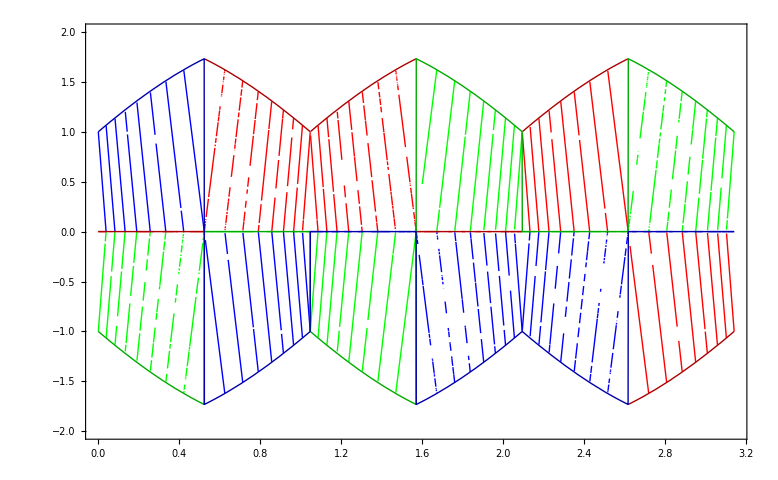

```mathematica
Show[{Plot[fYABError[θ,4,θ,2,1],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[fYABError[θ,4,θ,2,2],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[fYABError[θ,4,θ,2,3],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue],Plot[maxError[θ][[1]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Red]],Plot[maxError[θ][[2]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Green]],Plot[maxError[θ][[3]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Blue]]}]
```

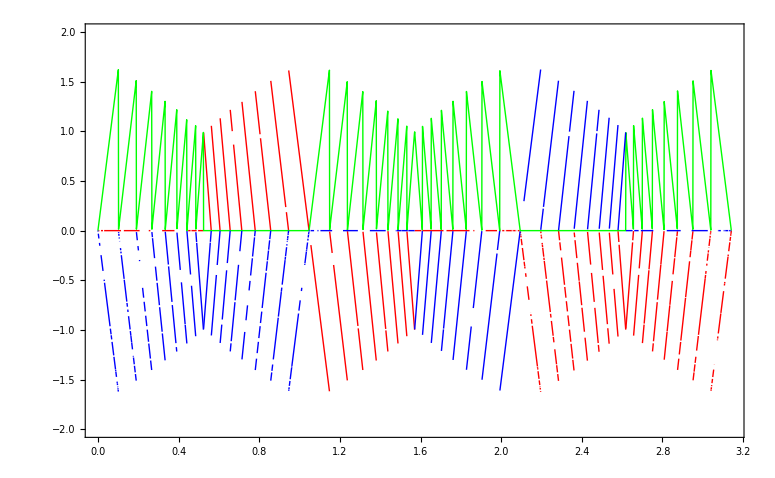

```mathematica
Show[{Plot[fYABError[θ,4,θ,3,1],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[fYABError[θ,4,θ,3,2],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[fYABError[θ,4,θ,3,3],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue]}]
```

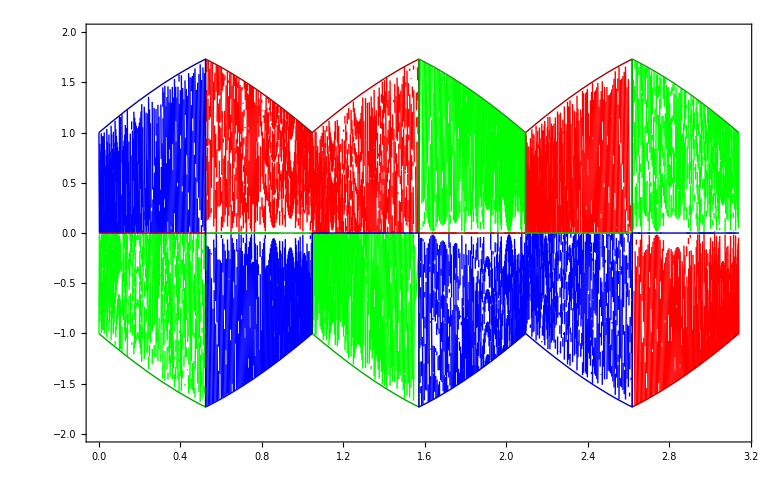

```mathematica
Show[{Plot[fYABError[θ,8,θ,2,1],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[fYABError[θ,8,θ,2,2],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[fYABError[θ,8,θ,2,3],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue],Plot[maxError[θ,θ][[2,1]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Red]],Plot[maxError[θ,θ][[2,2]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Green]],Plot[maxError[θ,θ][[2,3]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Blue]]}]
```

```mathematica
plotYABMaxError[n_,chan_]:=Module[{pts},
pts=Table[N[pointsIn[n,m,chan]],{m,0,6 2^( (n-1))}];Show[{Plot[fYABError[θ,n,θ,chan,1],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[fYABError[θ,n,θ,chan,2],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[fYABError[θ,n,θ,chan,3],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue],Plot[maxError[θ][[chan,1]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Red]],Plot[maxError[θ][[chan,2]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Green]],Plot[maxError[θ][[chan,3]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Blue]]
}]];
```

```mathematica
plotYABMaxError[n_,chan_]:=Module[{pts},
pts=Table[N[pointsIn[n,m,chan]],{m,0,6 2^( (n-1))}];Show[{Plot[fYABError[θ,n,θ,chan,1],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[fYABError[θ,n,θ,chan,2],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[fYABError[θ,n,θ,chan,3],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue],Plot[maxError[θ,θ][[chan,1]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Red]],Plot[maxError[θ,θ][[chan,2]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Green]],Plot[maxError[θ,θ][[chan,3]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Blue]],
ListPlot[pts[[All,1]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Red]],
ListPlot[pts[[All,2]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Green]],ListPlot[pts[[All,3]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Darker[Blue]]
}]];
```

```mathematica
chan3=plotYABMaxError[4,3];
chan2 = plotYABMaxError[4,2];
```

```mathematica
Table[N[pointsIn[3,m,3]],{m,0,6 2^( (3-1))}]
```

{{{0.,0.},{0.,1.},{0.,-1.}},{{0.190126,0.},{0.190126,1.51186},{0.190126,-1.51186}},{{0.333473,0.},{0.333473,1.30931},{0.333473,-1.30931}},{{0.441306,0.},{0.441306,1.13899},{0.441306,-1.13899}},{{1.0472,-1.},{1.0472,1.},{1.0472,0.}},{{0.857072,1.51186},{0.857072,0.},{0.857072,-1.51186}},{{0.713724,1.30931},{0.713724,0.},{0.713724,-1.30931}},{{0.605891,1.13899},{0.605891,0.},{0.605891,-1.13899}},{{1.0472,-1.},{1.0472,1.},{1.0472,0.}},{{1.23732,-1.51186},{1.23732,1.51186},{1.23732,0.}},{{1.38067,-1.30931},{1.38067,1.30931},{1.38067,0.}},{{1.4885,-1.13899},{1.4885,1.13899},{1.4885,0.}},{{2.0944,-1.},{2.0944,0.},{2.0944,1.}},{{1.90427,0.},{1.90427,1.51186},{1.90427,-1.51186}},{{1.76092,0.},{1.76092,1.30931},{1.76092,-1.30931}},{{1.65309,0.},{1.65309,1.13899},{1.65309,-1.13899}},{{2.0944,-1.},{2.0944,0.},{2.0944,1.}},{{2.28452,-1.51186},{2.28452,0.},{2.28452,1.51186}},{{2.42787,-1.30931},{2.42787,0.},{2.42787,1.30931}},{{2.5357,-1.13899},{2.5357,0.},{2.5357,1.13899}},{{3.14159,0.},{3.14159,1.},{3.14159,-1.}},{{2.95147,-1.51186},{2.95147,1.51186},{2.95147,0.}},{{2.80812,-1.30931},{2.80812,1.30931},{2.80812,0.}},{{2.70029,-1.13899},{2.70029,1.13899},{2.70029,0.}},{{3.14159,0.},{3.14159,1.},{3.14159,-1.}}}

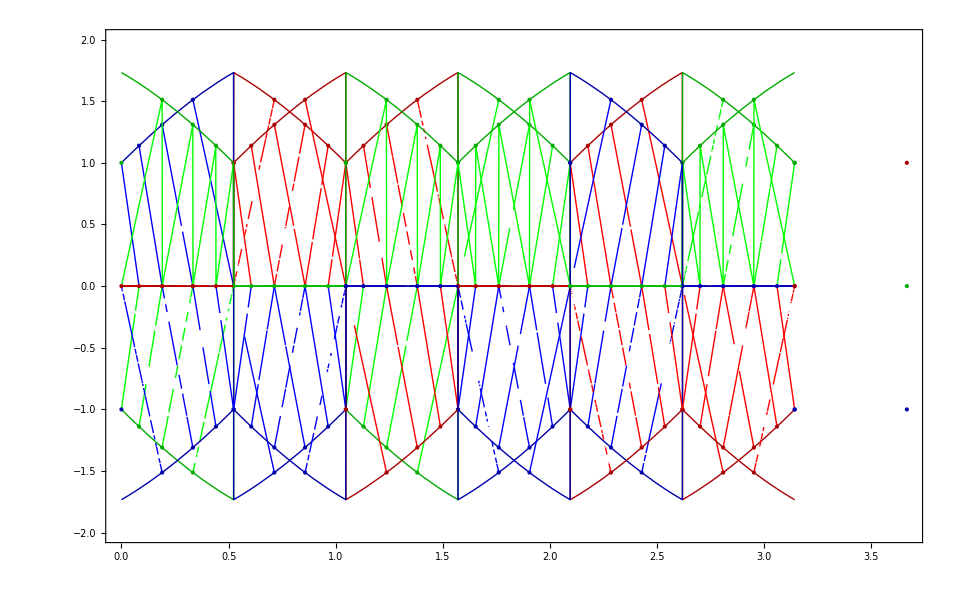

```mathematica
Show[{plotYABMaxError[3,2],plotYABMaxError[3,3]}]
```

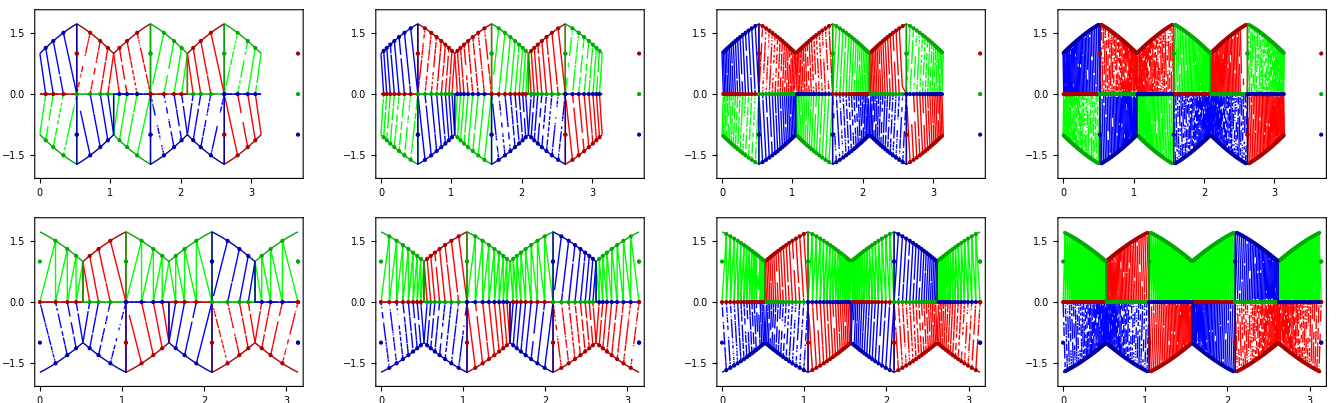

```mathematica
GraphicsGrid[{{plotYABMaxError[3,2],plotYABMaxError[4,2],plotYABMaxError[5,2],plotYABMaxError[6,2]},{plotYABMaxError[3,3],plotYABMaxError[4,3],plotYABMaxError[5,3],plotYABMaxError[6,3]}}]
```

```mathematica
fYABError[θ,n,Pi/12,3,2]/ maxError[θ,Pi/12][[3,2]]
```

1/2 Csc[π/6+Mod[-θ,π/6]] (-2 Cos[π/6+θ] IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]]+2^n Sin[θ])

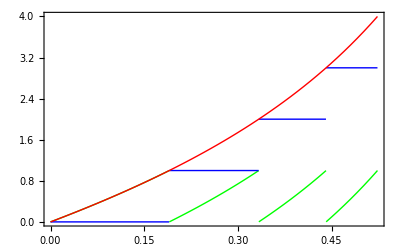

```mathematica
Plot[{1/2 Csc[π/6+Mod[-θ,π/6]] (-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ]),IntegerPart[4 Sec[π/6+θ] Sin[θ]],4 Sec[π/6+θ] Sin[θ]},{θ,0,Pi/6},PlotRange->{All,All},Frame -> True,PlotStyle->{Green,Blue,Red}]
```

```mathematica
Solve[2^(-1+n) Sec[π/6+θ] Sin[θ]==m,{θ}]
Assuming[m∈Integers&& m≥0&&n∈Integers&& n≥1&&0≤ θ ≤Pi/6,Simplify[%]]
```

{{θ→-ArcCos[-(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√(4 m^2+2 m Cosh[n Log[2]]+Cosh[n Log[2]]^2+2 m Sinh[n Log[2]]+2 Cosh[n Log[2]] Sinh[n Log[2]]+Sinh[n Log[2]]^2))]},{θ→ArcCos[-(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√(4 m^2+2 m Cosh[n Log[2]]+Cosh[n Log[2]]^2+2 m Sinh[n Log[2]]+2 Cosh[n Log[2]] Sinh[n Log[2]]+Sinh[n Log[2]]^2))]},{θ→-ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√(4 m^2+2 m Cosh[n Log[2]]+Cosh[n Log[2]]^2+2 m Sinh[n Log[2]]+2 Cosh[n Log[2]] Sinh[n Log[2]]+Sinh[n Log[2]]^2))]},{θ→ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√(4 m^2+2 m Cosh[n Log[2]]+Cosh[n Log[2]]^2+2 m Sinh[n Log[2]]+2 Cosh[n Log[2]] Sinh[n Log[2]]+Sinh[n Log[2]]^2))]}}

{{θ→-ArcCos[(-m-Cosh[n Log[2]]-Sinh[n Log[2]])/(√(4 m^2+2 m Cosh[n Log[2]]+Cosh[n Log[4]]+2 m Sinh[n Log[2]]+Sinh[n Log[4]]))]},{θ→ArcCos[(-m-Cosh[n Log[2]]-Sinh[n Log[2]])/(√(4 m^2+2 m Cosh[n Log[2]]+Cosh[n Log[4]]+2 m Sinh[n Log[2]]+Sinh[n Log[4]]))]},{θ→-ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√((Cosh[n Log[2]]+Sinh[n Log[2]]) (2 m+(1+4 m^2) Cosh[n Log[2]]+(1-4 m^2) Sinh[n Log[2]])))]},{θ→ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√((Cosh[n Log[2]]+Sinh[n Log[2]]) (2 m+(1+4 m^2) Cosh[n Log[2]]+(1-4 m^2) Sinh[n Log[2]])))]}}

```mathematica
Reduce[2^(-1+n) Sec[π/6+θ] Sin[θ]==m&&m∈Integers&& m≥0&&n∈Integers&& n≥1&&0≤ θ ≤Pi/6,{θ}]
```

Reduce[2^(-1+n) Sec[π/6+θ] Sin[θ]==m&&m∈Integers&&m≥0&&n∈Integers&&n≥1&&0≤θ≤π/6,{θ}]

```mathematica
Assuming[m∈Integers&& m≥0&&n∈Integers&& n≥1&&0≤ θ ≤Pi/6,Solve[4 Sec[π/6+θ] Sin[θ]==m,{θ}]]
```

{{θ→ConditionalExpression[ArcTan[-(8+m)/(√(64+16 m+4 m^2)),(-(8 √3 m)/(√(16+4 m+m^2))-(√3 m^2)/(√(16+4 m+m^2)))/(2 (8+m))]+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[ArcTan[(8+m)/(√(64+16 m+4 m^2)),((8 √3 m)/(√(16+4 m+m^2))+(√3 m^2)/(√(16+4 m+m^2)))/(2 (8+m))]+2 π C[1],C[1]∈Integers]}}

```mathematica
Assuming[m∈Integers&& m≥0&&n∈Integers&& n≥1,Simplify[ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√((Cosh[n Log[2]]+Sinh[n Log[2]]) (2 m+(1+4 m^2) Cosh[n Log[2]]+(1-4 m^2) Sinh[n Log[2]])))]]]
```

ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√((Cosh[n Log[2]]+Sinh[n Log[2]]) (2 m+(1+4 m^2) Cosh[n Log[2]]+(1-4 m^2) Sinh[n Log[2]])))]

```mathematica
Table[{2^(2(n-1)),2^n,Simplify[ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√((Cosh[n Log[2]]+Sinh[n Log[2]]) (2 m+(1+4 m^2) Cosh[n Log[2]]+(1-4 m^2) Sinh[n Log[2]])))]]},{n,1,8}]
```

{{1,2,ArcCos[(2+m)/(2 √(1+m+m^2))]},{4,4,ArcCos[(4+m)/(2 √(4+2 m+m^2))]},{16,8,ArcCos[(8+m)/(2 √(16+4 m+m^2))]},{64,16,ArcCos[(16+m)/(2 √(64+8 m+m^2))]},{256,32,ArcCos[(32+m)/(2 √(256+16 m+m^2))]},{1024,64,ArcCos[(64+m)/(2 √(1024+32 m+m^2))]},{4096,128,ArcCos[(128+m)/(2 √(4096+64 m+m^2))]},{16384,256,ArcCos[(256+m)/(2 √(16384+128 m+m^2))]}}

```mathematica
Factor[2^(2(n-1))+2^(n-1)  m+m^2]
```

1/4 (2^(2 n)+2^(1+n) m+4 m^2)

```mathematica
Expand[( m +b)^2]
```

b^2+2 b m+m^2

```mathematica
Expand[( m +2^(n-2))^2]
```

2^(-4+2 n)+2^(-1+n) m+m^2

```mathematica
OddQ[3]
```

True

```mathematica
Quotient[15,8]
```

1

```mathematica
Clear[pointsIn];
pointsIn[n_,m_,chan_]:=Module[{section,remainder,theta},
section = Quotient[m,2^(n-1)];
remainder = Mod[m,2^(n-1)];
theta=If[Xor[OddQ[section],chan==3],section Pi/6 + points[n,remainder],section Pi/6 +Pi/6-points[n,remainder]];
Map[List[theta,#1]&,maxError[theta,theta][[chan]]]
]
```

```mathematica
pointsIn[n_,m_,θ_]:=Module[{section,remainder},
section = Quotient[θ,Pi/6];
remainder = Mod[θ,Pi/6];
If[OddQ[section], points[n,m],Pi/6-points[n,m]]
];
```

```mathematica
pointsIn[n_,m_,Pi]
```

```mathematica
points[n_,m_]:=ArcCos[(2^n+m)/(2 √(2^(2(n-1))+2^(n-1)  m+m^2))];
points[n,m]
```

ArcCos[(2^n+m)/(2 √(2^(2 (-1+n))+2^(-1+n) m+m^2))]

```mathematica
Reverse[Pi/3-Table[N[points[nnn,m]],{m,0,2^(nnn-1)}]]
```

{0.523599,0.605891,0.713724,0.857072,1.0472}

```mathematica
Table[N[pointsIn[nnn,m,2]],{m,0,2^(2 (nnn-1))}]
```

{{{0.523599,1.},{0.523599,0.},{0.523599,-1.}},{{0.422064,0.},{0.422064,-1.62177},{0.422064,1.62177}},{{0.333473,0.},{0.333473,-1.51186},{0.333473,1.51186}},{{0.256645,0.},{0.256645,-1.4069},{0.256645,1.4069}},{{0.190126,0.},{0.190126,-1.30931},{0.190126,1.30931}},{{0.132455,0.},{0.132455,-1.21999},{0.132455,1.21999}},{{0.0822923,0.},{0.0822923,-1.13899},{0.0822923,1.13899}},{{0.038471,0.},{0.038471,-1.06588},{0.038471,1.06588}},{{0.523599,1.},{0.523599,0.},{0.523599,-1.}},{{0.625134,1.62177},{0.625134,0.},{0.625134,-1.62177}},{{0.713724,1.51186},{0.713724,0.},{0.713724,-1.51186}},{{0.790553,1.4069},{0.790553,0.},{0.790553,-1.4069}},{{0.857072,1.30931},{0.857072,0.},{0.857072,-1.30931}},{{0.914743,1.21999},{0.914743,0.},{0.914743,-1.21999}},{{0.964905,1.13899},{0.964905,0.},{0.964905,-1.13899}},{{1.00873,1.06588},{1.00873,0.},{1.00873,-1.06588}},{{1.5708,0.},{1.5708,1.},{1.5708,-1.}},{{1.46926,1.62177},{1.46926,-1.62177},{1.46926,0.}},{{1.38067,1.51186},{1.38067,-1.51186},{1.38067,0.}},{{1.30384,1.4069},{1.30384,-1.4069},{1.30384,0.}},{{1.23732,1.30931},{1.23732,-1.30931},{1.23732,0.}},{{1.17965,1.21999},{1.17965,-1.21999},{1.17965,0.}},{{1.12949,1.13899},{1.12949,-1.13899},{1.12949,0.}},{{1.08567,1.06588},{1.08567,-1.06588},{1.08567,0.}},{{1.5708,0.},{1.5708,1.},{1.5708,-1.}},{{1.67233,0.},{1.67233,1.62177},{1.67233,-1.62177}},{{1.76092,0.},{1.76092,1.51186},{1.76092,-1.51186}},{{1.83775,0.},{1.83775,1.4069},{1.83775,-1.4069}},{{1.90427,0.},{1.90427,1.30931},{1.90427,-1.30931}},{{1.96194,0.},{1.96194,1.21999},{1.96194,-1.21999}},{{2.0121,0.},{2.0121,1.13899},{2.0121,-1.13899}},{{2.05592,0.},{2.05592,1.06588},{2.05592,-1.06588}},{{2.61799,-1.},{2.61799,1.},{2.61799,0.}},{{2.51646,1.62177},{2.51646,0.},{2.51646,-1.62177}},{{2.42787,1.51186},{2.42787,0.},{2.42787,-1.51186}},{{2.35104,1.4069},{2.35104,0.},{2.35104,-1.4069}},{{2.28452,1.30931},{2.28452,0.},{2.28452,-1.30931}},{{2.22685,1.21999},{2.22685,0.},{2.22685,-1.21999}},{{2.17669,1.13899},{2.17669,0.},{2.17669,-1.13899}},{{2.13287,1.06588},{2.13287,0.},{2.13287,-1.06588}},{{2.61799,-1.},{2.61799,1.},{2.61799,0.}},{{2.71953,-1.62177},{2.71953,1.62177},{2.71953,0.}},{{2.80812,-1.51186},{2.80812,1.51186},{2.80812,0.}},{{2.88495,-1.4069},{2.88495,1.4069},{2.88495,0.}},{{2.95147,-1.30931},{2.95147,1.30931},{2.95147,0.}},{{3.00914,-1.21999},{3.00914,1.21999},{3.00914,0.}},{{3.0593,-1.13899},{3.0593,1.13899},{3.0593,0.}},{{3.10312,-1.06588},{3.10312,1.06588},{3.10312,0.}},{{3.66519,1.},{3.66519,0.},{3.66519,-1.}},{{3.56366,0.},{3.56366,-1.62177},{3.56366,1.62177}},{{3.47507,0.},{3.47507,-1.51186},{3.47507,1.51186}},{{3.39824,0.},{3.39824,-1.4069},{3.39824,1.4069}},{{3.33172,0.},{3.33172,-1.30931},{3.33172,1.30931}},{{3.27405,0.},{3.27405,-1.21999},{3.27405,1.21999}},{{3.22388,0.},{3.22388,-1.13899},{3.22388,1.13899}},{{3.18006,0.},{3.18006,-1.06588},{3.18006,1.06588}},{{3.66519,1.},{3.66519,0.},{3.66519,-1.}},{{3.76673,1.62177},{3.76673,0.},{3.76673,-1.62177}},{{3.85532,1.51186},{3.85532,0.},{3.85532,-1.51186}},{{3.93215,1.4069},{3.93215,0.},{3.93215,-1.4069}},{{3.99866,1.30931},{3.99866,0.},{3.99866,-1.30931}},{{4.05634,1.21999},{4.05634,0.},{4.05634,-1.21999}},{{4.1065,1.13899},{4.1065,0.},{4.1065,-1.13899}},{{4.15032,1.06588},{4.15032,0.},{4.15032,-1.06588}},{{4.71239,0.},{4.71239,1.},{4.71239,-1.}}}

```mathematica
Table[pts=N[pointsIn[nnn,m,2]];pts[[1]],{m,0,2^(2 (nnn-1))}]
```

{{0.523599,1.},{0.422064,0.},{0.333473,0.},{0.256645,0.},{0.190126,0.},{0.132455,0.},{0.0822923,0.},{0.038471,0.},{0.523599,1.},{0.625134,1.62177},{0.713724,1.51186},{0.790553,1.4069},{0.857072,1.30931},{0.914743,1.21999},{0.964905,1.13899},{1.00873,1.06588},{1.5708,0.},{1.46926,1.62177},{1.38067,1.51186},{1.30384,1.4069},{1.23732,1.30931},{1.17965,1.21999},{1.12949,1.13899},{1.08567,1.06588},{1.5708,0.},{1.67233,0.},{1.76092,0.},{1.83775,0.},{1.90427,0.},{1.96194,0.},{2.0121,0.},{2.05592,0.},{2.61799,-1.},{2.51646,1.62177},{2.42787,1.51186},{2.35104,1.4069},{2.28452,1.30931},{2.22685,1.21999},{2.17669,1.13899},{2.13287,1.06588},{2.61799,-1.},{2.71953,-1.62177},{2.80812,-1.51186},{2.88495,-1.4069},{2.95147,-1.30931},{3.00914,-1.21999},{3.0593,-1.13899},{3.10312,-1.06588},{3.66519,1.},{3.56366,0.},{3.47507,0.},{3.39824,0.},{3.33172,0.},{3.27405,0.},{3.22388,0.},{3.18006,0.},{3.66519,1.},{3.76673,1.62177},{3.85532,1.51186},{3.93215,1.4069},{3.99866,1.30931},{4.05634,1.21999},{4.1065,1.13899},{4.15032,1.06588},{4.71239,0.}}

```mathematica
pts[[All,1]]
```

{{0.523599,1.},{0.422064,0.},{0.333473,0.},{0.256645,0.},{0.190126,0.},{0.132455,0.},{0.0822923,0.},{0.038471,0.},{0.523599,1.},{0.625134,1.62177},{0.713724,1.51186},{0.790553,1.4069},{0.857072,1.30931},{0.914743,1.21999},{0.964905,1.13899},{1.00873,1.06588},{1.5708,0.},{1.46926,1.62177},{1.38067,1.51186},{1.30384,1.4069},{1.23732,1.30931},{1.17965,1.21999},{1.12949,1.13899},{1.08567,1.06588},{1.5708,0.},{1.67233,0.},{1.76092,0.},{1.83775,0.},{1.90427,0.},{1.96194,0.},{2.0121,0.},{2.05592,0.},{2.61799,-1.},{2.51646,1.62177},{2.42787,1.51186},{2.35104,1.4069},{2.28452,1.30931},{2.22685,1.21999},{2.17669,1.13899},{2.13287,1.06588},{2.61799,-1.},{2.71953,-1.62177},{2.80812,-1.51186},{2.88495,-1.4069},{2.95147,-1.30931},{3.00914,-1.21999},{3.0593,-1.13899},{3.10312,-1.06588},{3.66519,1.},{3.56366,0.},{3.47507,0.},{3.39824,0.},{3.33172,0.},{3.27405,0.},{3.22388,0.},{3.18006,0.},{3.66519,1.},{3.76673,1.62177},{3.85532,1.51186},{3.93215,1.4069},{3.99866,1.30931},{4.05634,1.21999},{4.1065,1.13899},{4.15032,1.06588},{4.71239,0.}}

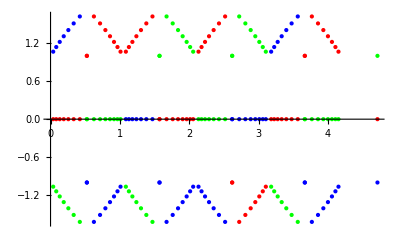

```mathematica
pts=Table[N[pointsIn[nnn,m,2]],{m,0,2^(2 (nnn-1))}];
Show[{ListPlot[pts[[All,1]],PlotStyle->Red],ListPlot[pts[[All,2]],PlotStyle->Green],ListPlot[pts[[All,3]],PlotStyle->Blue]}]
```

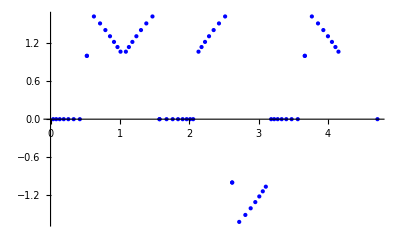

```mathematica
nnn=4;ListPlot[Table[pts=N[pointsIn[nnn,m,2]];pts[[1]],{m,0,2^(2 (nnn-1))}],PlotStyle->{Red,Green,Blue}]
```

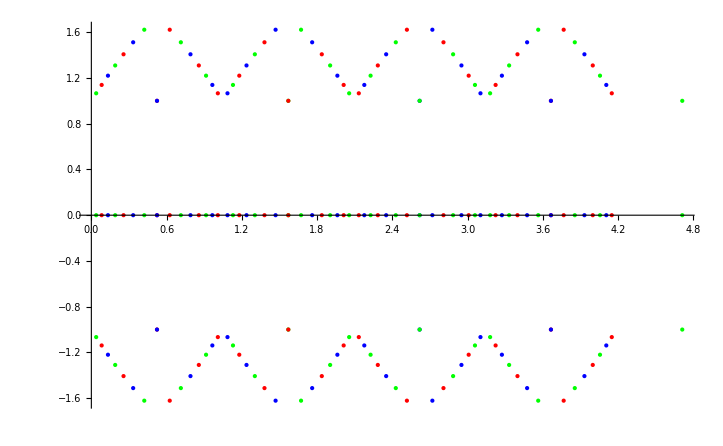

```mathematica
nnn=4;ListPlot[Table[pts=N[pointsIn[nnn,m,2]];{pts[[1]],pts[[2]],pts[[3]]},{m,0,2^(2 (nnn-1))}],PlotStyle->{Red,Green,Blue}]
```

```mathematica
Table[{points[n,m],Simplify[ArcCos[(m+Cosh[n Log[2]]+Sinh[n Log[2]])/(√((Cosh[n Log[2]]+Sinh[n Log[2]]) (2 m+(1+4 m^2) Cosh[n Log[2]]+(1-4 m^2) Sinh[n Log[2]])))]],m<2^(n-1)},{n,1,16}]
```

{{ArcCos[(2+m)/(2 √(1+m+m^2))],ArcCos[(2+m)/(2 √(1+m+m^2))],m<1},{ArcCos[(4+m)/(2 √(4+2 m+m^2))],ArcCos[(4+m)/(2 √(4+2 m+m^2))],m<2},{ArcCos[(8+m)/(2 √(16+4 m+m^2))],ArcCos[(8+m)/(2 √(16+4 m+m^2))],m<4},{ArcCos[(16+m)/(2 √(64+8 m+m^2))],ArcCos[(16+m)/(2 √(64+8 m+m^2))],m<8},{ArcCos[(32+m)/(2 √(256+16 m+m^2))],ArcCos[(32+m)/(2 √(256+16 m+m^2))],m<16},{ArcCos[(64+m)/(2 √(1024+32 m+m^2))],ArcCos[(64+m)/(2 √(1024+32 m+m^2))],m<32},{ArcCos[(128+m)/(2 √(4096+64 m+m^2))],ArcCos[(128+m)/(2 √(4096+64 m+m^2))],m<64},{ArcCos[(256+m)/(2 √(16384+128 m+m^2))],ArcCos[(256+m)/(2 √(16384+128 m+m^2))],m<128},{ArcCos[(512+m)/(2 √(65536+256 m+m^2))],ArcCos[(512+m)/(2 √(65536+256 m+m^2))],m<256},{ArcCos[(1024+m)/(2 √(262144+512 m+m^2))],ArcCos[(1024+m)/(2 √(262144+512 m+m^2))],m<512},{ArcCos[(2048+m)/(2 √(1048576+1024 m+m^2))],ArcCos[(2048+m)/(2 √(1048576+1024 m+m^2))],m<1024},{ArcCos[(4096+m)/(2 √(4194304+2048 m+m^2))],ArcCos[(4096+m)/(2 √(4194304+2048 m+m^2))],m<2048},{ArcCos[(8192+m)/(2 √(16777216+4096 m+m^2))],ArcCos[(8192+m)/(2 √(16777216+4096 m+m^2))],m<4096},{ArcCos[(16384+m)/(2 √(67108864+8192 m+m^2))],ArcCos[(16384+m)/(2 √(67108864+8192 m+m^2))],m<8192},{ArcCos[(32768+m)/(2 √(268435456+16384 m+m^2))],ArcCos[(32768+m)/(2 √(268435456+16384 m+m^2))],m<16384},{ArcCos[(65536+m)/(2 √(1073741824+32768 m+m^2))],ArcCos[(65536+m)/(2 √(1073741824+32768 m+m^2))],m<32768}}

```mathematica
Table[Table[N[points[nnn,m]],{m,0,2^(nnn-1)}],{nnn,1,8}]
```

{{0.,0.523599},{0.,0.333473,0.523599},{0.,0.190126,0.333473,0.441306,0.523599},{0.,0.101535,0.190126,0.266954,0.333473,0.391144,0.441306,0.485128,0.523599},{0.,0.0524383,0.101535,0.147385,0.190126,0.229922,0.266954,0.301409,0.333473,0.363327,0.391144,0.417087,0.441306,0.463944,0.485128,0.504977,0.523599},{0.,0.0266406,0.0524383,0.0773996,0.101535,0.124858,0.147385,0.169134,0.190126,0.210381,0.229922,0.248772,0.266954,0.284492,0.301409,0.317729,0.333473,0.348665,0.363327,0.37748,0.391144,0.40434,0.417087,0.429403,0.441306,0.452815,0.463944,0.47471,0.485128,0.495212,0.504977,0.514435,0.523599},{0.,0.0134259,0.0266406,0.0396445,0.0524383,0.0650229,0.0773996,0.0895697,0.101535,0.113297,0.124858,0.13622,0.147385,0.158356,0.169134,0.179723,0.190126,0.200344,0.210381,0.220239,0.229922,0.239432,0.248772,0.257945,0.266954,0.275802,0.284492,0.293027,0.301409,0.309642,0.317729,0.325671,0.333473,0.341137,0.348665,0.356061,0.363327,0.370466,0.37748,0.384372,0.391144,0.397799,0.40434,0.410768,0.417087,0.423297,0.429403,0.435405,0.441306,0.447109,0.452815,0.458426,0.463944,0.469371,0.47471,0.479961,0.485128,0.490211,0.495212,0.500134,0.504977,0.509743,0.514435,0.519053,0.523599},{0.,0.0067394,0.0134259,0.0200597,0.0266406,0.0331689,0.0396445,0.0460676,0.0524383,0.0587567,0.0650229,0.0712372,0.0773996,0.0835104,0.0895697,0.0955779,0.101535,0.107441,0.113297,0.119103,0.124858,0.130564,0.13622,0.141827,0.147385,0.152894,0.158356,0.163769,0.169134,0.174452,0.179723,0.184948,0.190126,0.195258,0.200344,0.205385,0.210381,0.215332,0.220239,0.225102,0.229922,0.234698,0.239432,0.244123,0.248772,0.253379,0.257945,0.26247,0.266954,0.271398,0.275802,0.280167,0.284492,0.288779,0.293027,0.297237,0.301409,0.305544,0.309642,0.313703,0.317729,0.321718,0.325671,0.32959,0.333473,0.337322,0.341137,0.344918,0.348665,0.35238,0.356061,0.35971,0.363327,0.366912,0.370466,0.373988,0.37748,0.380941,0.384372,0.387773,0.391144,0.394486,0.397799,0.401084,0.40434,0.407568,0.410768,0.413941,0.417087,0.420205,0.423297,0.426363,0.429403,0.432417,0.435405,0.438368,0.441306,0.44422,0.447109,0.449974,0.452815,0.455632,0.458426,0.461196,0.463944,0.466669,0.469371,0.472051,0.47471,0.477346,0.479961,0.482555,0.485128,0.48768,0.490211,0.492722,0.495212,0.497683,0.500134,0.502565,0.504977,0.507369,0.509743,0.512098,0.514435,0.516753,0.519053,0.521335,0.523599}}

```mathematica
Table[N[ArcCos[(8+m)/(2 √(16+4 m+m^2))]],{m,0,4}]
```

{0.,0.190126,0.333473,0.441306,0.523599}

```mathematica
Table[N[ArcTan[(8+n)/(√(64+16 n+4 n^2)),((8 √3 n)/(√(16+4 n+n^2))+(√3 n^2)/(√(16+4 n+n^2)))/(2 (8+n))]],{n,0,4}]
```

{0.,0.190126,0.333473,0.441306,0.523599}

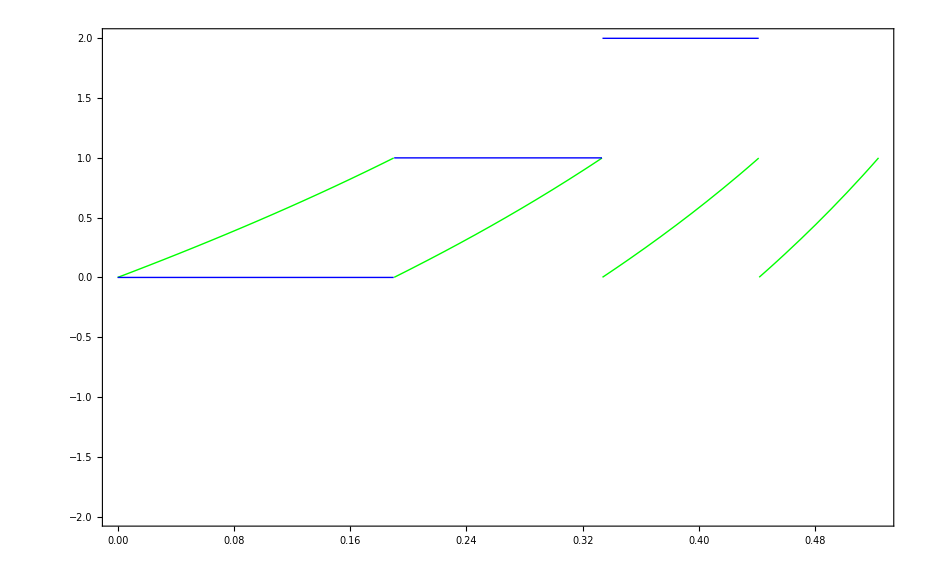

```mathematica
Plot[{1/2 Csc[π/6+Mod[-θ,π/6]] (-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ]),IntegerPart[4 Sec[π/6+θ] Sin[θ]]},{θ,0,Pi/6},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{Green,Blue}]
```

```mathematica
-2 Cos[π/6] IntegerPart[4 Sec[π/6] Sin[0]]+8 Sin[0]
-2 Cos[π/6+π/6] IntegerPart[4 Sec[π/6+π/6] Sin[π/6]]+8 Sin[π/6]
```

0

0

```mathematica
Solve[fYABError[θ,3,θ,3,2]<10^-6&&0<θ<Pi/6,θ]
```

Solve[(Piecewise[{{-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ], 0<θ<π/6}, {0, π/6<θ<π/3}, {-2 Cos[π/6-θ] IntegerPart[(8 Sin[θ])/(√3 Cos[θ]+Sin[θ])]+8 Sin[θ], π/3<θ<π/2}, {-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ], π/2<θ<(2 π)/3}, {0, (2 π)/3<θ<(5 π)/6}, {-2 Cos[π/6-θ] IntegerPart[(8 Sin[θ])/(√3 Cos[θ]+Sin[θ])]+8 Sin[θ], (5 π)/6<θ<π}, {Null, True}}])<1/1000000&&0<θ<π/6,θ]

```mathematica
Solve[-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ]==0&&0<θ<Pi/6,{θ}]
```

Solve[-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ]==0&&0<θ<π/6,{θ}]

```mathematica
NSolve[-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ]<10^-6&&0<θ<π/6,{θ}]
```

NSolve[-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ]<1/1000000&&0<θ<π/6,{θ}]

```mathematica
Union[Table[θ/.FindRoot[-2 Cos[π/6+θ] IntegerPart[4 Sec[π/6+θ] Sin[θ]]+8 Sin[θ],{θ,n Pi/72}],{n,1,12}]]
```

{0.,0.190126,0.190126,0.333473,0.333473,0.441306,0.523599}

```mathematica
{0.,0.190126,0.333473,0.333473,0.523599}
```

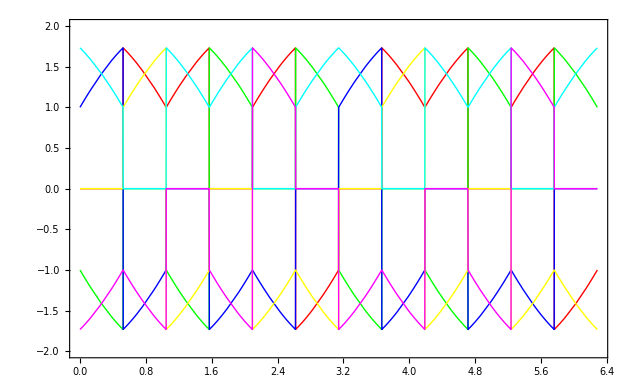

```mathematica
partMaxErrorFun[θ_]:=2 Sin[Mod[θ,Pi/6]+Pi/6];
maxError[θ_,ϕ_] :=Piecewise[{
{{{0,0,0},{0,- partMaxErrorFun[θ],partMaxErrorFun[θ]},{0, partMaxErrorFun[-θ],-partMaxErrorFun[-θ]}},0≤Mod[ϕ,Pi]<Pi/6},
{{{0,0,0},{partMaxErrorFun[-θ],0,-partMaxErrorFun[-θ]},{partMaxErrorFun[θ],0,-partMaxErrorFun[θ]}},Pi/6≤Mod[ϕ,Pi]<2Pi/6},
{{{0,0,0},{partMaxErrorFun[θ],- partMaxErrorFun[θ],0},{-partMaxErrorFun[-θ],partMaxErrorFun[-θ],0}},2Pi/6≤Mod[ϕ,Pi]<3 Pi/6},
{{{0,0,0},{0,partMaxErrorFun[-θ],-partMaxErrorFun[-θ]},{0,partMaxErrorFun[θ],-partMaxErrorFun[θ]}},3 Pi/6≤Mod[ϕ,Pi]<4 Pi/6},
{{{0,0,0},{partMaxErrorFun[θ],0,-partMaxErrorFun[θ]},{-partMaxErrorFun[-θ],0,partMaxErrorFun[-θ]}},4 Pi/6≤Mod[ϕ,Pi]<5 Pi/6},
{{{0,0,0},{-partMaxErrorFun[-θ],partMaxErrorFun[-θ],0},{-partMaxErrorFun[θ],partMaxErrorFun[θ],0}},5 Pi/6≤Mod[ϕ,Pi]<Pi}}];
Show[{Plot[maxError[θ,θ][[2,1]],{θ,0,2Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[maxError[θ,θ][[2,2]],{θ,0,2Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[maxError[θ,θ][[2,3]],{θ,0,2Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue],Plot[maxError[θ,θ][[3,1]],{θ,0,2Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Yellow],Plot[maxError[θ,θ][[3,2]],{θ,0,2Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Cyan],Plot[maxError[θ,θ][[3,3]],{θ,0,2Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle-> Magenta]}]
```

```mathematica
maxError[θ].{r,g,b}
```

(Piecewise[{{{{0,0,0},{0,-2 Sin[π/6+Mod[θ,π/6]],2 Sin[π/6+Mod[θ,π/6]]},{0,2 Sin[π/6+Mod[-θ,π/6]],-2 Sin[π/6+Mod[-θ,π/6]]}}, 0≤θ<π/6}, {{{0,0,0},{2 Sin[π/6+Mod[-θ,π/6]],0,-2 Sin[π/6+Mod[-θ,π/6]]},{2 Sin[π/6+Mod[θ,π/6]],0,-2 Sin[π/6+Mod[θ,π/6]]}}, π/6≤θ<π/3}, {{{0,0,0},{2 Sin[π/6+Mod[θ,π/6]],-2 Sin[π/6+Mod[θ,π/6]],0},{-2 Sin[π/6+Mod[-θ,π/6]],2 Sin[π/6+Mod[-θ,π/6]],0}}, π/3≤θ<π/2}, {{{0,0,0},{0,2 Sin[π/6+Mod[-θ,π/6]],-2 Sin[π/6+Mod[-θ,π/6]]},{0,2 Sin[π/6+Mod[θ,π/6]],-2 Sin[π/6+Mod[θ,π/6]]}}, π/2≤θ<(2 π)/3}, {{{0,0,0},{2 Sin[π/6+Mod[θ,π/6]],0,-2 Sin[π/6+Mod[θ,π/6]]},{-2 Sin[π/6+Mod[-θ,π/6]],0,2 Sin[π/6+Mod[-θ,π/6]]}}, (2 π)/3≤θ<(5 π)/6}, {{{0,0,0},{-2 Sin[π/6+Mod[-θ,π/6]],2 Sin[π/6+Mod[-θ,π/6]],0},{-2 Sin[π/6+Mod[θ,π/6]],2 Sin[π/6+Mod[θ,π/6]],0}}, (5 π)/6≤θ<π}, {0, True}}]).{r,g,b}

```mathematica
PiecewiseExpand[maxError[θ,ϕ].{r,g,b}]
```

Piecewise[{{0.{r,g,b}, Mod[ϕ,π]≥π||Mod[ϕ,π]<0}, {{0,-2 b Sin[π/6+Mod[-θ,π/6]]+2 g Sin[π/6+Mod[-θ,π/6]],-2 b Sin[π/6+Mod[θ,π/6]]+2 g Sin[π/6+Mod[θ,π/6]]}, π/2≤Mod[ϕ,π]<(2 π)/3}, {{0,2 g Sin[π/6+Mod[-θ,π/6]]-2 r Sin[π/6+Mod[-θ,π/6]],2 g Sin[π/6+Mod[θ,π/6]]-2 r Sin[π/6+Mod[θ,π/6]]}, (5 π)/6≤Mod[ϕ,π]<π}, {{0,-2 b Sin[π/6+Mod[-θ,π/6]]+2 r Sin[π/6+Mod[-θ,π/6]],-2 b Sin[π/6+Mod[θ,π/6]]+2 r Sin[π/6+Mod[θ,π/6]]}, π/6≤Mod[ϕ,π]<π/3}, {{0,2 b Sin[π/6+Mod[θ,π/6]]-2 g Sin[π/6+Mod[θ,π/6]],-2 b Sin[π/6+Mod[-θ,π/6]]+2 g Sin[π/6+Mod[-θ,π/6]]}, 0≤Mod[ϕ,π]<π/6}, {{0,-2 b Sin[π/6+Mod[θ,π/6]]+2 r Sin[π/6+Mod[θ,π/6]],2 b Sin[π/6+Mod[-θ,π/6]]-2 r Sin[π/6+Mod[-θ,π/6]]}, (2 π)/3≤Mod[ϕ,π]<(5 π)/6}, {{0,-2 g Sin[π/6+Mod[θ,π/6]]+2 r Sin[π/6+Mod[θ,π/6]],2 g Sin[π/6+Mod[-θ,π/6]]-2 r Sin[π/6+Mod[-θ,π/6]]}, True}}]

```mathematica
Collect[%,{r,g,b}]
```

```mathematica
Piecewise[{{0.{r,g,b}, θ≥π||θ<0}, {{0,-2 b Cos[π/6-θ]+2 g Cos[π/6-θ],2 b Cos[π/6+θ]-2 g Cos[π/6+θ]}, θ==π/2}, {{0,2 b Cos[θ]-2 r Cos[θ],2 b Sin[θ]-2 r Sin[θ]}, (2 π)/3<θ<(5 π)/6}, {{0,2 b Cos[θ]-2 r Cos[θ],2 b Sin[π/6+θ]-2 r Sin[π/6+θ]}, θ==(2 π)/3}, {{0,-2 b Cos[θ]+2 r Cos[θ],-2 b Sin[θ]+2 r Sin[θ]}, π/6<θ<π/3}, {{0,-2 b Cos[π/6+θ]+2 r Cos[π/6+θ],-2 b Sin[θ]+2 r Sin[θ]}, θ==π/6}, {{0,2 g Sin[π/6-θ]-2 r Sin[π/6-θ],2 g Cos[π/6-θ]-2 r Cos[π/6-θ]}, π/3<θ<π/2}, {{0,2 g Sin[π/6-θ]-2 r Sin[π/6-θ],2 g Cos[θ]-2 r Cos[θ]}, θ==π/3}, {{0,-2 g Sin[π/6-θ]+2 r Sin[π/6-θ],-2 g Cos[π/6-θ]+2 r Cos[π/6-θ]}, (5 π)/6<θ<π}, {{0,2 g Sin[θ]-2 r Sin[θ],-2 g Cos[π/6-θ]+2 r Cos[π/6-θ]}, θ==(5 π)/6}, {{0,2 b Sin[π/6+θ]-2 g Sin[π/6+θ],-2 b Cos[π/6+θ]+2 g Cos[π/6+θ]}, 0<θ<π/6}, {{0,2 b Sin[π/6+θ]-2 g Sin[π/6+θ],-2 b Sin[π/6-θ]+2 g Sin[π/6-θ]}, θ==0}, {{0,-2 b Sin[π/6+θ]+2 g Sin[π/6+θ],2 b Cos[π/6+θ]-2 g Cos[π/6+θ]}, True}}]
```

```mathematica
Piecewise[{{{0,2 (-b+g) Cos[π/6-θ],2 (b-g) Cos[π/6+θ]}, θ==π/2}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[θ]}, (2 π)/3<θ<(5 π)/6}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[π/6+θ]}, θ==(2 π)/3}, {{0,2 (-b+r) Cos[θ],2 (-b+r) Sin[θ]}, π/6<θ<π/3}, {{0,2 (-b+r) Cos[π/6+θ],2 (-b+r) Sin[θ]}, θ==π/6}, {{0,2 (g-r) Sin[π/6-θ],2(g-r)  Cos[π/6-θ]}, π/3<θ<π/2}, {{0,2 (g-r) Sin[π/6-θ],2 (g-r) Cos[θ]}, θ==π/3}, {{0,2 (-g+r) Sin[π/6-θ],2 (-g+r) Cos[π/6-θ]}, (5 π)/6<θ<π}, {{0,2 (g-r) Sin[θ],2 (-g+r) Cos[π/6-θ]}, θ==(5 π)/6}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Cos[π/6+θ]}, 0<θ<π/6}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Sin[π/6-θ]}, θ==0}, {{0,2 (-b+g) Sin[π/6+θ],2 (b-g) Cos[π/6+θ]}, π/2≤θ<(2 π)/3}}]
```

```mathematica
Piecewise[{{{0,2 (-b+g) Cos[π/6-θ],2 (b-g) Cos[π/6+θ]}, θ==π/2}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[θ]}, (2 π)/3<θ<(5 π)/6}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[π/6+θ]}, θ==(2 π)/3}, {{0,2 (-b+r) Cos[θ],2 (-b+r) Sin[θ]}, π/6<θ<π/3}, {{0,2 (-b+r) Cos[π/6+θ],2 (-b+r) Sin[θ]}, θ==π/6}, {{0,2 (g-r) Sin[π/6-θ],2(g-r)  Cos[π/6-θ]}, π/3<θ<π/2}, {{0,2 (g-r) Sin[π/6-θ],2 (g-r) Cos[θ]}, θ==π/3}, {{0,2 (-g+r) Sin[π/6-θ],2 (-g+r) Cos[π/6-θ]}, (5 π)/6<θ<π}, {{0,2 (g-r) Sin[θ],2 (-g+r) Cos[π/6-θ]}, θ==(5 π)/6}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Cos[π/6+θ]}, 0<θ<π/6}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Sin[π/6-θ]}, θ==0}, {{0,2 (-b+g) Sin[π/6+θ],2 (b-g) Cos[π/6+θ]}, π/2≤θ<(2 π)/3}}]
```

Piecewise[{{{0,2 (-b+g) Cos[π/6-θ],2 (b-g) Cos[π/6+θ]}, θ==π/2}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[θ]}, (2 π)/3<θ<(5 π)/6}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[π/6+θ]}, θ==(2 π)/3}, {{0,2 (-b+r) Cos[θ],2 (-b+r) Sin[θ]}, π/6<θ<π/3}, {{0,2 (-b+r) Cos[π/6+θ],2 (-b+r) Sin[θ]}, θ==π/6}, {{0,2 (g-r) Sin[π/6-θ],2 (g-r) Cos[π/6-θ]}, π/3<θ<π/2}, {{0,2 (g-r) Sin[π/6-θ],2 (g-r) Cos[θ]}, θ==π/3}, {{0,2 (-g+r) Sin[π/6-θ],2 (-g+r) Cos[π/6-θ]}, (5 π)/6<θ<π}, {{0,2 (g-r) Sin[θ],2 (-g+r) Cos[π/6-θ]}, θ==(5 π)/6}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Cos[π/6+θ]}, 0<θ<π/6}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Sin[π/6-θ]}, θ==0}, {{0,2 (-b+g) Sin[π/6+θ],2 (b-g) Cos[π/6+θ]}, π/2≤θ<(2 π)/3}, {0, True}}]

```mathematica
TrigReduce[Simplify[%]]
```

Piecewise[{{0.{r,g,b}, Mod[ϕ,π]≥π||Mod[ϕ,π]<0}, {{0,2 (-b+g) Sin[π/6+Mod[-θ,π/6]],2 (-b+g) Sin[π/6+Mod[θ,π/6]]}, π/2≤Mod[ϕ,π]<(2 π)/3}, {{0,2 (g-r) Sin[π/6+Mod[-θ,π/6]],2 (g-r) Sin[π/6+Mod[θ,π/6]]}, (5 π)/6≤Mod[ϕ,π]<π}, {{0,2 (-b+r) Sin[π/6+Mod[-θ,π/6]],2 (-b+r) Sin[π/6+Mod[θ,π/6]]}, π/6≤Mod[ϕ,π]<π/3}, {{0,2 (b-g) Sin[π/6+Mod[θ,π/6]],2 (-b+g) Sin[π/6+Mod[-θ,π/6]]}, 0≤Mod[ϕ,π]<π/6}, {{0,2 (-b+r) Sin[π/6+Mod[θ,π/6]],2 (b-r) Sin[π/6+Mod[-θ,π/6]]}, (2 π)/3≤Mod[ϕ,π]<(5 π)/6}, {{0,2 (-g+r) Sin[π/6+Mod[θ,π/6]],2 (g-r) Sin[π/6+Mod[-θ,π/6]]}, True}}]

```mathematica
InputForm[%]
```

Piecewise[{{{0, 2*(-b + g)*Cos[Pi/6 - θ], 2*(b - g)*Cos[Pi/6 + θ]}, θ == Pi/2}, {{0, 2*(b - r)*Cos[θ], 2*(b - r)*Sin[θ]}, 
   (2*Pi)/3 < θ < (5*Pi)/6}, {{0, 2*(b - r)*Cos[θ], 2*(b - r)*Sin[Pi/6 + θ]}, θ == (2*Pi)/3}, 
  {{0, 2*(-b + r)*Cos[θ], 2*(-b + r)*Sin[θ]}, Pi/6 < θ < Pi/3}, {{0, 2*(-b + r)*Cos[Pi/6 + θ], 2*(-b + r)*Sin[θ]}, θ == Pi/6}, 
  {{0, 2*(g - r)*Sin[Pi/6 - θ], 2*(g - r)*Cos[Pi/6 - θ]}, Pi/3 < θ < Pi/2}, {{0, 2*(g - r)*Sin[Pi/6 - θ], 2*(g - r)*Cos[θ]}, θ == Pi/3}, 
  {{0, 2*(-g + r)*Sin[Pi/6 - θ], 2*(-g + r)*Cos[Pi/6 - θ]}, (5*Pi)/6 < θ < Pi}, {{0, 2*(g - r)*Sin[θ], 2*(-g + r)*Cos[Pi/6 - θ]}, 
   θ == (5*Pi)/6}, {{0, 2*(b - g)*Sin[Pi/6 + θ], 2*(-b + g)*Cos[Pi/6 + θ]}, 0 < θ < Pi/6}, 
  {{0, 2*(b - g)*Sin[Pi/6 + θ], 2*(-b + g)*Sin[Pi/6 - θ]}, θ == 0}, {{0, 2*(-b + g)*Sin[Pi/6 + θ], 2*(b - g)*Cos[Pi/6 + θ]}, 
   Inequality[Pi/2, LessEqual, θ, Less, (2*Pi)/3]}}, 0]

```mathematica
RGBmaxError[θ_]:=Piecewise[{
{{0,2*(  b-g)*Sin[Pi/6],2*(-b+g)*Sin[Pi/6]},θ==0},
{{0,2*(  b-g)*Sin[Pi/6+θ],2*(-b+g)*Cos[Pi/6+θ]},0<θ<Pi/6},
{{0,2*(-b+r)*Cos[Pi/6+Pi/6],2*(-b+r)*Sin[Pi/6]},θ==Pi/6},
{{0,2*(-b+r)*Cos[θ],2*(-b+r)*Sin[θ]},Pi/6<θ<Pi/3},
{{0,2*(  g-r)*Sin[Pi/6-Pi/3],2*(g-r)*Cos[Pi/3]},θ==Pi/3},
{{0,2*(  g-r)*Sin[Pi/6-θ],2*(g-r)*Cos[Pi/6-θ]},Pi/3<θ<Pi/2},
{{0,2*(-b+g)*Cos[Pi/6-Pi/2],2*(b-g)*Cos[Pi/6+Pi/2]},θ==Pi/2},
{{0,2*(-b+g)*Sin[Pi/6+θ],2*(b-g)*Cos[Pi/6+θ]},Pi/2 ≤ θ < 2 Pi/3},
{{0,2*(  b-r)*Cos[(2*Pi)/3],2*(b-r)*Sin[Pi/6+(2*Pi)/3]},θ==(2*Pi)/3},
{{0,2*(  b-r)*Cos[θ],2*(b-r)*Sin[θ]},(2*Pi)/3<θ<(5*Pi)/6},
{{0,2*(  g-r)*Sin[(5*Pi)/6],2*(-g+r)*Cos[Pi/6-(5*Pi)/6]},θ==(5*Pi)/6},
{{0,2*(-g+r)*Sin[Pi/6-θ],2*(-g+r)*Cos[Pi/6-θ]},(5*Pi)/6<θ<Pi}
},0]
```

```mathematica
RGBmaxError[θ]
```

Piecewise[{{{0,b-g,-b+g}, θ==0}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Cos[π/6+θ]}, 0<θ<π/6}, {{0,-b+r,-b+r}, θ==π/6}, {{0,2 (-b+r) Cos[θ],2 (-b+r) Sin[θ]}, π/6<θ<π/3}, {{0,-g+r,g-r}, θ==π/3}, {{0,2 (g-r) Sin[π/6-θ],2 (g-r) Cos[π/6-θ]}, π/3<θ<π/2}, {{0,-b+g,-b+g}, θ==π/2}, {{0,2 (-b+g) Sin[π/6+θ],2 (b-g) Cos[π/6+θ]}, π/2≤θ<(2 π)/3}, {{0,-b+r,b-r}, θ==(2 π)/3}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[θ]}, (2 π)/3<θ<(5 π)/6}, {{0,g-r,g-r}, θ==(5 π)/6}, {{0,2 (-g+r) Sin[π/6-θ],2 (-g+r) Cos[π/6-θ]}, (5 π)/6<θ<π}, {0, True}}]

```mathematica
Simplify[PiecewiseExpand[maxError[θ].{r,g,b}]]
```

Piecewise[{{0.{r,g,b}, θ≥π||θ<0}, {{0,2 (-b+g) Cos[1/6 (π-6 θ)],2 (b-g) Cos[π/6+θ]}, 2 θ==π}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[θ]}, (2 π)/3<θ<(5 π)/6}, {{0,2 (b-r) Cos[θ],2 (b-r) Sin[π/6+θ]}, 3 θ==2 π}, {{0,2 (-b+r) Cos[θ],2 (-b+r) Sin[θ]}, π/6<θ<π/3}, {{0,2 (-b+r) Cos[π/6+θ],2 (-b+r) Sin[θ]}, 6 θ==π}, {{0,2 (g-r) Sin[1/6 (π-6 θ)],(g-r) (√3 Cos[θ]+Sin[θ])}, π/3<θ<π/2}, {{0,2 (g-r) Sin[1/6 (π-6 θ)],2 (g-r) Cos[θ]}, 3 θ==π}, {{0,2 (-g+r) Sin[1/6 (π-6 θ)],2 (-g+r) Cos[1/6 (π-6 θ)]}, (5 π)/6<θ<π}, {{0,2 (g-r) Sin[θ],2 (-g+r) Cos[1/6 (π-6 θ)]}, 6 θ==5 π}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Cos[π/6+θ]}, θ>0&&6 θ<π}, {{0,2 (b-g) Sin[π/6+θ],2 (-b+g) Sin[1/6 (π-6 θ)]}, θ==0}, {{0,2 (-b+g) Sin[π/6+θ],2 (b-g) Cos[π/6+θ]}, True}}]

```mathematica
partMaxErrorFun[θ_]:=2 Sin[Mod[θ,Pi/6]+Pi/6];
maxError[θ_] :=Piecewise[{
{{0,- partMaxErrorFun[θ],partMaxErrorFun[θ]},0≤θ<Pi/6},
{{partMaxErrorFun[-θ],0,-partMaxErrorFun[-θ]},Pi/6≤θ<2Pi/6},
{{partMaxErrorFun[θ],- partMaxErrorFun[θ],0},2Pi/6≤θ<3 Pi/6},
{{0,partMaxErrorFun[-θ],-partMaxErrorFun[-θ]},3 Pi/6≤θ<4 Pi/6},
{{partMaxErrorFun[θ],0,-partMaxErrorFun[θ]},4 Pi/6≤θ<5 Pi/6},
{{-partMaxErrorFun[-θ],partMaxErrorFun[-θ],0},5 Pi/6≤θ<Pi}}];
```

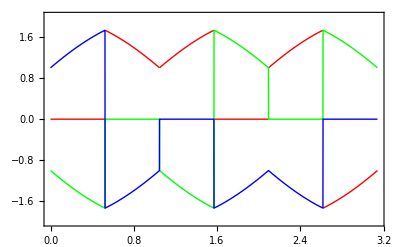

```mathematica
Show[{Plot[maxError[θ][[1]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Red],Plot[maxError[θ][[2]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Green],Plot[maxError[θ][[3]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->Blue]}]
```

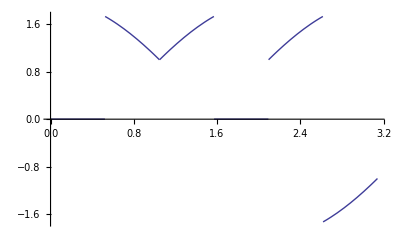

```mathematica
Plot[maxError[θ][[1]],{θ,0,Pi}]
```

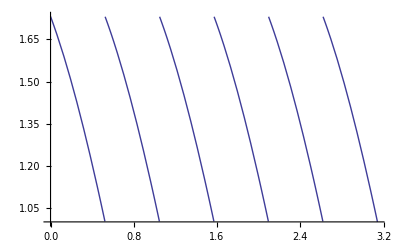

```mathematica
Plot[partMaxErrorFun[-θ],{θ,0,Pi}]
```

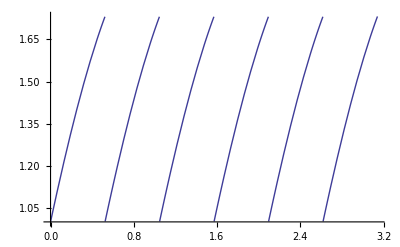

```mathematica
Plot[2 Sin[Mod[θ,Pi/6]+Pi/6],{θ,0,Pi}]
```

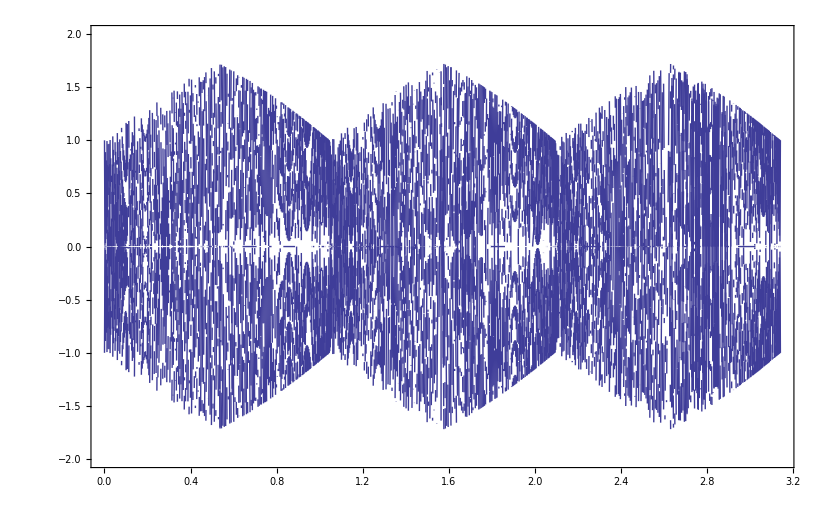

```mathematica
Plot[fYABError[θ,8,θ,2,All],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True]
```

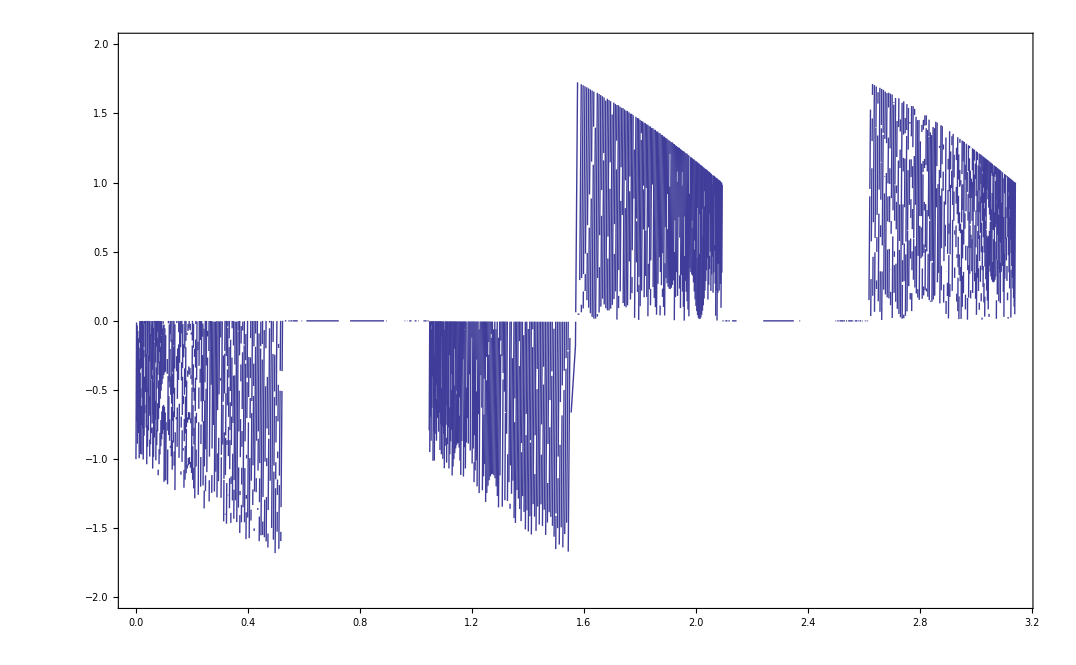

```mathematica
Plot[fYABError[θ,8,θ,2,2],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True]
```

```mathematica
Plot[Evaluate[Union[Flatten[fYABError[θ,8,θ]]]],{θ,0,Pi},PlotRange->{All,{-2,2}},Frame -> True]
```

-Graphics-

```mathematica
Definition[fYABError]
```

fYABError=Function[{θ,n,ψ},Piecewise[{{{{0,0,0},{0,-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^n Sin[π/6-θ]-2 IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]},{0,-2 Cos[π/6+θ] IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]]+2^n Sin[θ],-2^n Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]}}, cyclicSolve[0<ψ<π/6,n]}, {{{0,0,0},{-2 Cos[θ] IntegerPart[2^(-1+n) Sec[θ] Sin[π/6+θ]]+2^n Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[2^(-1+n) Sec[θ] Sin[π/6-θ]]+2^n Sin[π/6-θ]},{2^n Cos[π/6+θ]-2 IntegerPart[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ],0,-2^n Cos[π/6-θ]+2 IntegerPart[2^(-2+n) (1+√3 Cot[θ])] Sin[θ]}}, cyclicSolve[π/6<ψ<π/3,n]}, {{{0,0,0},{-2 IntegerPart[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+2^n Sin[π/6+θ],-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0},{2^n Cos[π/6+θ]-2 Cos[π/6-θ] IntegerPart[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]],-2 Cos[π/6-θ] IntegerPart[(2^n Sin[θ])/(√3 Cos[θ]+Sin[θ])]+2^n Sin[θ],0}}, cyclicSolve[π/3<ψ<π/2,n]}, {{{0,0,0},{0,-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^n Sin[π/6-θ]-2 IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]},{0,-2 Cos[π/6+θ] IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]]+2^n Sin[θ],-2^n Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]}}, cyclicSolve[π/2<ψ<(2 π)/3,n]}, {{{0,0,0},{-2 Cos[θ] IntegerPart[2^(-1+n) Sec[θ] Sin[π/6+θ]]+2^n Sin[π/6+θ],0,-2 Cos[θ] IntegerPart[2^(-1+n) Sec[θ] Sin[π/6-θ]]+2^n Sin[π/6-θ]},{2^n Cos[π/6+θ]-2 IntegerPart[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ],0,-2^n Cos[π/6-θ]+2 IntegerPart[2^(-2+n) (1+√3 Cot[θ])] Sin[θ]}}, cyclicSolve[(2 π)/3<ψ<(5 π)/6,n]}, {{{0,0,0},{-2 IntegerPart[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+2^n Sin[π/6+θ],-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ],0},{2^n Cos[π/6+θ]-2 Cos[π/6-θ] IntegerPart[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]],-2 Cos[π/6-θ] IntegerPart[(2^n Sin[θ])/(√3 Cos[θ]+Sin[θ])]+2^n Sin[θ],0}}, cyclicSolve[(5 π)/6<ψ<π,n]}, {Null, True}}]]

```mathematica
YABError[θ_,n_,ψ_] := 2^n (YABDiscretFactor[θ,2^n,ψ]IntegerPart[fYAB[θ,2^n,ψ]] . RGBCube- rYAB[θ] . RGBCube);

vals=Function[{θ,n},Evaluate[Assuming[Element[n,Integers]&& n≥1,Simplify[YABError[θ,n,Pi/12]]]]];
MatrixForm[vals[θ,n] ]
MatrixForm[Union[Flatten[vals[θ,n]]]]
Plot[Union[Flatten[vals[θ,8]]],{θ,0,Pi/6},PlotRange->{All,{-2,2}},Frame -> True]
```

```mathematica
Union[Flatten[vals[θ,n]]]
```

{0,-2^n Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]],2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 (2^n+2 IntegerPart[(2^n Sin[θ])/(√3 Cos[θ]-Sin[θ])]) (√3 Cos[θ]-Sin[θ]),2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] (IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]])+Sin[θ]),-2 Cos[π/6+θ] IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]]+2^n Sin[θ],-1/2 (2^n-2 IntegerPart[(2^n Cos[θ])/(Cos[θ]+√3 Sin[θ])]+2 IntegerPart[(2^(-1+n) (Cos[θ]-√3 Sin[θ]))/(Cos[θ]+√3 Sin[θ])]) (Cos[θ]+√3 Sin[θ]),-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^n (-Cos[θ]+Sin[π/6-θ]+2^(1-n) (IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]]-IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]) Sin[π/6+θ]),2^n Sin[π/6-θ]-2 IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]}

```mathematica
n=8
Plot[{0,-2^n Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]],2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 (2^n+2 IntegerPart[(2^n Sin[θ])/(√3 Cos[θ]-Sin[θ])]) (√3 Cos[θ]-Sin[θ]),2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] (IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]])+Sin[θ]),-2 Cos[π/6+θ] IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]]+2^n Sin[θ],-1/2 (2^n-2 IntegerPart[(2^n Cos[θ])/(Cos[θ]+√3 Sin[θ])]+2 IntegerPart[(2^(-1+n) (Cos[θ]-√3 Sin[θ]))/(Cos[θ]+√3 Sin[θ])]) (Cos[θ]+√3 Sin[θ]),-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^n (-Cos[θ]+Sin[π/6-θ]+2^(1-n) (IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]]-IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]) Sin[π/6+θ]),2^n Sin[π/6-θ]-2 IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]},{θ,0,Pi/6},PlotRange->{All,{-2,2}},Frame -> True,PlotLegends->Automatic,MaxRecursion->15]
```

8

-Graphics-

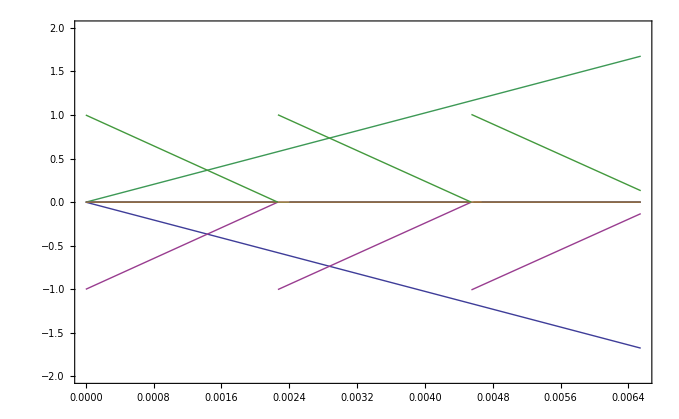

```mathematica
Plot[{-2^n Cos[π/6-θ]+2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]],2 Cos[π/6+θ] IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 (2^n+2 IntegerPart[(2^n Sin[θ])/(√3 Cos[θ]-Sin[θ])]) (√3 Cos[θ]-Sin[θ]),2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] (IntegerPart[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]])+Sin[θ]),-2 Cos[π/6+θ] IntegerPart[2^(-1+n) Sec[π/6+θ] Sin[θ]]+2^n Sin[θ],-1/2 (2^n-2 IntegerPart[(2^n Cos[θ])/(Cos[θ]+√3 Sin[θ])]+2 IntegerPart[(2^(-1+n) (Cos[θ]-√3 Sin[θ]))/(Cos[θ]+√3 Sin[θ])]) (Cos[θ]+√3 Sin[θ]),-2^n Cos[θ]+2 IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ],2^n (-Cos[θ]+Sin[π/6-θ]+2^(1-n) (IntegerPart[2^(-1+n) Cos[θ] Csc[π/6+θ]]-IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]) Sin[π/6+θ]),2^n Sin[π/6-θ]-2 IntegerPart[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]},{θ,0,Pi/480},PlotRange->{All,{-2,2}},Frame -> True]
```

```mathematica
Assuming[Element[n,Integers]&& n≥1,FullSimplify[IntegerPart[2^(-1+n)]]]
```

2^(-1+n)

```mathematica
MatrixForm[RGBCube]
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
TableForm[Table[
{MatrixForm[ fYAB[θ-Pi/12+δθ,1,θ]],inPiBySixRegion[θ,θ+δθ],θ} ,{θ,Pi/12,Pi,Pi/6}]]
```

(1 | 1 | 1
1/2 | -1/2 Cos[δθ] Csc[π/6+δθ] | 1/2 Csc[π/6+δθ] Sin[π/6-δθ]
1/2 | 1/2 Sec[π/6+δθ] Sin[δθ] | -1/2 Cos[π/6-δθ] Sec[π/6+δθ]) | TraditionalForm`0 < TraditionalForm`δθ + π/12 < TraditionalForm`π/6 | π/12
(1 | 1 | 1
-1/2 Cos[π/6-δθ] Sec[π/6+δθ] | 1/2 | 1/2 Sec[π/6+δθ] Sin[δθ]
1/2 Csc[π/6+δθ] Sin[π/6-δθ] | 1/2 | -1/2 Cos[δθ] Csc[π/6+δθ]) | TraditionalForm`π/6 < TraditionalForm`δθ + π/4 < TraditionalForm`π/3 | π/4
(1 | 1 | 1
-1/2 Cos[δθ] Csc[π/6+δθ] | 1/2 Csc[π/6+δθ] Sin[π/6-δθ] | 1/2
1/2 Sec[π/6+δθ] Sin[δθ] | -1/2 Cos[π/6-δθ] Sec[π/6+δθ] | 1/2) | TraditionalForm`π/3 < TraditionalForm`δθ + 5\ π/12 < TraditionalForm`π/2 | (5 π)/12
(1 | 1 | 1
1/2 | 1/2 Sec[π/6+δθ] Sin[δθ] | -1/2 Cos[π/6-δθ] Sec[π/6+δθ]
1/2 | -1/2 Cos[δθ] Csc[π/6+δθ] | 1/2 Csc[π/6+δθ] Sin[π/6-δθ]) | TraditionalForm`π/2 < TraditionalForm`δθ + 7\ π/12 < TraditionalForm`2\ π/3 | (7 π)/12
(1 | 1 | 1
1/2 Csc[π/6+δθ] Sin[π/6-δθ] | 1/2 | -1/2 Cos[δθ] Csc[π/6+δθ]
-1/2 Cos[π/6-δθ] Sec[π/6+δθ] | 1/2 | 1/2 Sec[π/6+δθ] Sin[δθ]) | TraditionalForm`2\ π/3 < TraditionalForm`δθ + 3\ π/4 < TraditionalForm`5\ π/6 | (3 π)/4
(1 | 1 | 1
1/2 Sec[π/6+δθ] Sin[δθ] | -1/2 Cos[π/6-δθ] Sec[π/6+δθ] | 1/2
-1/2 Cos[δθ] Csc[π/6+δθ] | 1/2 Csc[π/6+δθ] Sin[π/6-δθ] | 1/2) | TraditionalForm`5\ π/6 < TraditionalForm`δθ + 11\ π/12 < TraditionalForm`π | (11 π)/12

```mathematica
YABDiscretFactor[θ,2^n,θ] IntegerPart[fYAB[θ,2^n,θ]] - rYAB[θ]
```

{{-1+IntegerPart[{ | «1»] (Piecewise[{{{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, n π<θ<π/6+n π/.FindInstance[n π<θ<π/6+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, π/6+n π<θ<π/3+n π/.FindInstance[π/6+n π<θ<π/3+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, π/3+n π<θ<π/2+n π/.FindInstance[π/3+n π<θ<π/2+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, π/2+n π<θ<(2 π)/3+n π/.FindInstance[π/2+n π<θ<(2 π)/3+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, (2 π)/3+n π<θ<(5 π)/6+n π/.FindInstance[(2 π)/3+n π<θ<(5 π)/6+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, «1»/.«1»}, {Null, «4»}}]),-1+IntegerPart[{ | «1»] ({ | «1»),-1+IntegerPart[{ | «1»] ({ | «1»)},{IntegerPart[{ | «1»] ({ | «1»)+Sin[π/6+θ],-Cos[θ]+IntegerPart[{ | «1»] ({ | «1»),IntegerPart[{ | «1»] ({ | «1»)+Sin[π/6-θ]},{Cos[π/6+θ]+IntegerPart[{ | «1»] ({ | «1»),IntegerPart[{ | «1»] ({ | «1»)+Sin[θ],-Cos[π/6-θ]+IntegerPart[{ | «1»] ({ | «1»)}}

```mathematica
FullSimplify[YABDiscretFactor[θ,2^n,θ] IntegerPart[fYAB[θ,2^n,θ]] - rYAB[θ]]
```

{{{ | «1»,{ | «1»,{ | «1»},{IntegerPart[{ | «1»] (Piecewise[{{{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, n π<θ<π/6+n π/.FindInstance[n π<θ<π/6+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, π/6+n π<θ<π/3+n π/.FindInstance[π/6+n π<θ<π/3+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, π/3+n π<θ<π/2+n π/.FindInstance[π/3+n π<θ<π/2+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, π/2+n π<θ<(2 π)/3+n π/.FindInstance[π/2+n π<θ<(2 π)/3+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, (2 π)/3+n π<θ<(5 π)/6+n π/.FindInstance[(2 π)/3+n π<θ<(5 π)/6+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, (5 π)/6+n π<θ<π+n π/.FindInstance[(5 π)/6+n π<θ<π+n π&&n∈Integers,n]}, {Null, True}}])+Sin[π/6+θ],{ | «1»,IntegerPart[{ | «1»] (Piecewise[{{{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, n π<θ<π/6+n π/.FindInstance[n π<θ<π/6+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, π/6+n π<θ<π/3+n π/.FindInstance[π/6+n π<θ<π/3+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, π/3+n π<θ<π/2+n π/.FindInstance[π/3+n π<θ<π/2+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, π/2+n π<θ<(2 π)/3+n π/.FindInstance[π/2+n π<θ<(2 π)/3+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, (2 π)/3+n π<θ<(5 π)/6+n π/.FindInstance[(2 π)/3+n π<θ<(5 π)/6+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, (5 π)/6+n π<θ<π+n π/.FindInstance[(5 π)/6+n π<θ<π+n π&&n∈Integers,n]}, {Null, True}}])+Sin[1/6 (π-6 θ)]},{Cos[π/6+θ]+IntegerPart[Piecewise[{{{{1,1,1},{2^(-1+n),-2^(-1+n) Cos[θ] Csc[π/6+θ],2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]},{2^(-1+n),2^(-1+n) Sec[π/6+θ] Sin[θ],-2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]}}, (n π<θ<(1/6+n) π/.FindInstance[n π<θ<(1/6+n) π&&n∈Integers,n])||(!((1/6+n) π<θ<(1/3+n) π/.FindInstance[(1/6+n) π<θ<(1/3+n) π&&n∈Integers,n])&&!((1/3+n) π<θ<(1/2+n) π/.FindInstance[(1/3+n) π<θ<(1/2+n) π&&n∈Integers,n])&&((1/2+n) π<θ<(2/3+n) π/.FindInstance[(1/2+n) π<θ<(2/3+n) π&&n∈Integers,n]))}, {{{1,1,1},{-2^(-1+n) Sec[θ] Sin[π/6+θ],2^(-1+n),2^(-2+n) (-1+√3 Tan[θ])},{2^(-1+n) Cos[π/6+θ] Csc[θ],2^(-1+n),-2^(-2+n) (1+√3 Cot[θ])}}, ((1/6+n) π<θ<(1/3+n) π/.FindInstance[(1/6+n) π<θ<(1/3+n) π&&n∈Integers,n])||(!((1/3+n) π<θ<(1/2+n) π/.FindInstance[(1/3+n) π<θ<(1/2+n) π&&n∈Integers,n])&&!((1/2+n) π<θ<(2/3+n) π/.FindInstance[(1/2+n) π<θ<(2/3+n) π&&n∈Integers,n])&&((2/3+n) π<θ<(5/6+n) π/.FindInstance[(2/3+n) π<θ<(5/6+n) π&&n∈Integers,n]))}, {{{1,1,1},{2^(-1+n) Csc[π/6-θ] Sin[π/6+θ],-2^(-1+n) Cos[θ] Csc[π/6-θ],2^(-1+n)},{-2^(-1+n) Cos[π/6+θ] Sec[π/6-θ],-2^n/(1+√3 Cot[θ]),2^(-1+n)}}, ((1/3+n) π<θ<(1/2+n) π/.FindInstance[(1/3+n) π<θ<(1/2+n) π&&n∈Integers,n])||(!((1/2+n) π<θ<(2/3+n) π/.FindInstance[«1»,n])&&!(«1»)&&(«1»))}, {Null, «1»}}]] (Piecewise[{{{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, n π<θ<π/6+n π/.FindInstance[n π<θ<π/6+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, π/6+n π<θ<π/3+n π/.FindInstance[π/6+n π<θ<π/3+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, π/3+n π<θ<π/2+n π/.FindInstance[π/3+n π<θ<π/2+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, π/2+n π<θ<(2 π)/3+n π/.FindInstance[π/2+n π<θ<(2 π)/3+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, (2 π)/3+n π<θ<(5 π)/6+n π/.FindInstance[(2 π)/3+n π<θ<(5 π)/6+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, (5 π)/6+n π<θ<π+n π/.FindInstance[(5 π)/6+n π<θ<π+n π&&n∈Integers,n]}, {Null, True}}]),{ | «1»,-Cos[1/6 (π-6 θ)]+IntegerPart[{ | «1»] (Piecewise[{{{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, n π<θ<π/6+n π/.FindInstance[n π<θ<π/6+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, π/6+n π<θ<π/3+n π/.FindInstance[π/6+n π<θ<π/3+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, π/3+n π<θ<π/2+n π/.FindInstance[π/3+n π<θ<π/2+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6+θ],-2^(1-n) Cos[π/6+θ]}, π/2+n π<θ<(2 π)/3+n π/.FindInstance[π/2+n π<θ<(2 π)/3+n π&&n∈Integers,n]}, {{1,2^(1-n) Cos[θ],-2^(1-n) Sin[θ]}, (2 π)/3+n π<θ<(5 π)/6+n π/.FindInstance[(2 π)/3+n π<θ<(5 π)/6+n π&&n∈Integers,n]}, {{1,-2^(1-n) Sin[π/6-θ],2^(1-n) Cos[π/6-θ]}, (5 π)/6+n π<θ<π+n π/.FindInstance[(5 π)/6+n π<θ<π+n π&&n∈Integers,n]}, {Null, True}}])}}

```mathematica
MatrixForm[Table[mat = (((Sign[Sign[rYAB[θ]].{1,1,1}] Sign[rYAB[θ]] +1)/2));factor=Function[{ϕ},Evaluate[({1/3,2,2}  mat Map[If[#≥1/2,1,0]&,Abs[rYAB[θ]],{2}] rYAB[ϕ]).{1,1,1}]];
fYAB[θ_] :=rYAB[θ]/factor[θ];
{MatrixForm[factor[ϕ]],MatrixForm[fYAB[ϕ]],MatrixForm[TrigReduce[FullSimplify[TrigExpand[fYAB[ϕ]]]]],MatrixForm[factor[θ]],MatrixForm[N[fYAB[θ]]],MatrixForm[rYAB[θ]],MatrixForm[rYAB[θ+δθ]],MatrixForm[mat],(mat.{r,g,b})[[2]]<1 && (mat.{r,g,b})[[3]]<1,inPiBySixRegaion[θ],θ} ,{θ,Pi/12,Pi,Pi/6}]]
```

((1
-2 Sin[π/6+ϕ]
-2 Cos[π/6+ϕ]) | (1 | 1 | 1
1/2 | -1/2 Cos[ϕ] Csc[π/6+ϕ] | 1/2 Csc[π/6+ϕ] Sin[π/6-ϕ]
1/2 | 1/2 Sec[π/6+ϕ] Sin[ϕ] | -1/2 Cos[π/6-ϕ] Sec[π/6+ϕ]) | (1 | 1 | 1
1/2 | -1/(1+√3 Tan[ϕ]) | (Cos[ϕ]-√3 Sin[ϕ])/(2 (Cos[ϕ]+√3 Sin[ϕ]))
1/2 | 1/(-1+√3 Cot[ϕ]) | (-√3 Cos[ϕ]-Sin[ϕ])/(2 (√3 Cos[ϕ]-Sin[ϕ]))) | (1
-√2
-√2) | (1. | 1. | 1.
0.5 | -0.683013 | 0.183013
0.5 | 0.183013 | -0.683013) | (1 | 1 | 1
-1/(√2) | (1+√3)/(2 √2) | -(-1+√3)/(2 √2)
-1/(√2) | -(-1+√3)/(2 √2) | (1+√3)/(2 √2)) | (1 | 1 | 1
-Sin[π/4+δθ] | Cos[π/12+δθ] | -Sin[π/12-δθ]
-Cos[π/4+δθ] | -Sin[π/12+δθ] | Cos[π/12-δθ]) | (1 | 1 | 1
1 | 0 | 1
1 | 1 | 0) | b+r<1&&g+r<1 | TraditionalForm`0 < θ < TraditionalForm`π/6 | π/12
(1
2 Cos[ϕ]
-2 Sin[ϕ]) | (1 | 1 | 1
-1/2 Sec[ϕ] Sin[π/6+ϕ] | 1/2 | -1/2 Sec[ϕ] Sin[π/6-ϕ]
1/2 Cos[π/6+ϕ] Csc[ϕ] | 1/2 | -1/2 Cos[π/6-ϕ] Csc[ϕ]) | (1 | 1 | 1
1/4 (-1-√3 Tan[ϕ]) | 1/2 | 1/4 (-1+√3 Tan[ϕ])
1/4 (-1+√3 Cot[ϕ]) | 1/2 | 1/4 (-1-√3 Cot[ϕ])) | (1
√2
-√2) | (1. | 1. | 1.
-0.683013 | 0.5 | 0.183013
0.183013 | 0.5 | -0.683013) | (1 | 1 | 1
-(1+√3)/(2 √2) | 1/(√2) | (-1+√3)/(2 √2)
-(-1+√3)/(2 √2) | -1/(√2) | (1+√3)/(2 √2)) | (1 | 1 | 1
-Cos[π/12-δθ] | Cos[π/4+δθ] | Sin[π/12+δθ]
-Sin[π/12-δθ] | -Sin[π/4+δθ] | Cos[π/12+δθ]) | (1 | 1 | 1
0 | 1 | 1
1 | 1 | 0) | b+g<1&&g+r<1 | TraditionalForm`π/6 < θ < TraditionalForm`π/3 | π/4
(1
-2 Sin[π/6-ϕ]
2 Cos[π/6-ϕ]) | (1 | 1 | 1
1/2 Csc[π/6-ϕ] Sin[π/6+ϕ] | -1/2 Cos[ϕ] Csc[π/6-ϕ] | 1/2
-1/2 Cos[π/6+ϕ] Sec[π/6-ϕ] | -1/2 Sec[π/6-ϕ] Sin[ϕ] | 1/2) | (1 | 1 | 1
(Cos[ϕ]+√3 Sin[ϕ])/(2 (Cos[ϕ]-√3 Sin[ϕ])) | 1/(-1+√3 Tan[ϕ]) | 1/2
(-√3 Cos[ϕ]+Sin[ϕ])/(2 (√3 Cos[ϕ]+Sin[ϕ])) | -1/(1+√3 Cot[ϕ]) | 1/2) | (1
√2
√2) | (1. | 1. | 1.
-0.683013 | 0.183013 | 0.5
0.183013 | -0.683013 | 0.5) | (1 | 1 | 1
-(1+√3)/(2 √2) | (-1+√3)/(2 √2) | 1/(√2)
(-1+√3)/(2 √2) | -(1+√3)/(2 √2) | 1/(√2)) | (1 | 1 | 1
-Cos[π/12+δθ] | Sin[π/12-δθ] | Sin[π/4+δθ]
Sin[π/12+δθ] | -Cos[π/12-δθ] | Cos[π/4+δθ]) | (1 | 1 | 1
0 | 1 | 1
1 | 0 | 1) | b+g<1&&b+r<1 | TraditionalForm`π/3 < θ < TraditionalForm`π/2 | (5 π)/12
(1
-2 Sin[π/6+ϕ]
-2 Cos[π/6+ϕ]) | (1 | 1 | 1
1/2 | -1/2 Cos[ϕ] Csc[π/6+ϕ] | 1/2 Csc[π/6+ϕ] Sin[π/6-ϕ]
1/2 | 1/2 Sec[π/6+ϕ] Sin[ϕ] | -1/2 Cos[π/6-ϕ] Sec[π/6+ϕ]) | (1 | 1 | 1
1/2 | -1/(1+√3 Tan[ϕ]) | (Cos[ϕ]-√3 Sin[ϕ])/(2 (Cos[ϕ]+√3 Sin[ϕ]))
1/2 | 1/(-1+√3 Cot[ϕ]) | (-√3 Cos[ϕ]-Sin[ϕ])/(2 (√3 Cos[ϕ]-Sin[ϕ]))) | (1
-√2
√2) | (1. | 1. | 1.
0.5 | 0.183013 | -0.683013
0.5 | -0.683013 | 0.183013) | (1 | 1 | 1
-1/(√2) | -(-1+√3)/(2 √2) | (1+√3)/(2 √2)
1/(√2) | -(1+√3)/(2 √2) | (-1+√3)/(2 √2)) | (1 | 1 | 1
-Sin[π/4-δθ] | -Sin[π/12+δθ] | Cos[π/12-δθ]
Cos[π/4-δθ] | -Cos[π/12+δθ] | Sin[π/12-δθ]) | (1 | 1 | 1
1 | 1 | 0
1 | 0 | 1) | g+r<1&&b+r<1 | TraditionalForm`π/2 < θ < TraditionalForm`2\ π/3 | (7 π)/12
(1
2 Cos[ϕ]
-2 Sin[ϕ]) | (1 | 1 | 1
-1/2 Sec[ϕ] Sin[π/6+ϕ] | 1/2 | -1/2 Sec[ϕ] Sin[π/6-ϕ]
1/2 Cos[π/6+ϕ] Csc[ϕ] | 1/2 | -1/2 Cos[π/6-ϕ] Csc[ϕ]) | (1 | 1 | 1
1/4 (-1-√3 Tan[ϕ]) | 1/2 | 1/4 (-1+√3 Tan[ϕ])
1/4 (-1+√3 Cot[ϕ]) | 1/2 | 1/4 (-1-√3 Cot[ϕ])) | (1
-√2
-√2) | (1. | 1. | 1.
0.183013 | 0.5 | -0.683013
-0.683013 | 0.5 | 0.183013) | (1 | 1 | 1
-(-1+√3)/(2 √2) | -1/(√2) | (1+√3)/(2 √2)
(1+√3)/(2 √2) | -1/(√2) | -(-1+√3)/(2 √2)) | (1 | 1 | 1
-Sin[π/12-δθ] | -Cos[π/4-δθ] | Cos[π/12+δθ]
Cos[π/12-δθ] | -Sin[π/4-δθ] | -Sin[π/12+δθ]) | (1 | 1 | 1
1 | 1 | 0
0 | 1 | 1) | g+r<1&&b+g<1 | TraditionalForm`2\ π/3 < θ < TraditionalForm`5\ π/6 | (3 π)/4
(1
-2 Sin[π/6-ϕ]
2 Cos[π/6-ϕ]) | (1 | 1 | 1
1/2 Csc[π/6-ϕ] Sin[π/6+ϕ] | -1/2 Cos[ϕ] Csc[π/6-ϕ] | 1/2
-1/2 Cos[π/6+ϕ] Sec[π/6-ϕ] | -1/2 Sec[π/6-ϕ] Sin[ϕ] | 1/2) | (1 | 1 | 1
(Cos[ϕ]+√3 Sin[ϕ])/(2 (Cos[ϕ]-√3 Sin[ϕ])) | 1/(-1+√3 Tan[ϕ]) | 1/2
(-√3 Cos[ϕ]+Sin[ϕ])/(2 (√3 Cos[ϕ]+Sin[ϕ])) | -1/(1+√3 Cot[ϕ]) | 1/2) | (1
√2
-√2) | (1. | 1. | 1.
0.183013 | -0.683013 | 0.5
-0.683013 | 0.183013 | 0.5) | (1 | 1 | 1
(-1+√3)/(2 √2) | -(1+√3)/(2 √2) | 1/(√2)
(1+√3)/(2 √2) | -(-1+√3)/(2 √2) | -1/(√2)) | (1 | 1 | 1
Sin[π/12+δθ] | -Cos[π/12-δθ] | Sin[π/4-δθ]
Cos[π/12+δθ] | -Sin[π/12-δθ] | -Cos[π/4-δθ]) | (1 | 1 | 1
1 | 0 | 1
0 | 1 | 1) | b+r<1&&b+g<1 | TraditionalForm`5\ π/6 < θ < TraditionalForm`π | (11 π)/12)

```mathematica
Clear[errorFree]
errorFree =Function[{pt,θ},Evaluate[Piecewise[Table[mat = (((Sign[Sign[rYAB[ϕ]].{1,1,1}] Sign[rYAB[ϕ]] +1)/2).{pt[[1]],pt[[2]],pt[[3]]});{mat[[2]]<1 && mat[[3]]<1,cSol[ToExpression[inPiBySixRegaion[ϕ]],n] } ,{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
Definition[errorFree]
```

errorFree=Function[{pt,θ},Piecewise[{{pt⟦1⟧+pt⟦3⟧<1&&pt⟦1⟧+pt⟦2⟧<1, cyclicSolve[0<θ<π/6,n]}, {pt⟦2⟧+pt⟦3⟧<1&&pt⟦1⟧+pt⟦2⟧<1, cyclicSolve[π/6<θ<π/3,n]}, {pt⟦2⟧+pt⟦3⟧<1&&pt⟦1⟧+pt⟦3⟧<1, cyclicSolve[π/3<θ<π/2,n]}, {pt⟦1⟧+pt⟦2⟧<1&&pt⟦1⟧+pt⟦3⟧<1, cyclicSolve[π/2<θ<(2 π)/3,n]}, {pt⟦1⟧+pt⟦2⟧<1&&pt⟦2⟧+pt⟦3⟧<1, cyclicSolve[(2 π)/3<θ<(5 π)/6,n]}, {pt⟦1⟧+pt⟦3⟧<1&&pt⟦2⟧+pt⟦3⟧<1, cyclicSolve[(5 π)/6<θ<π,n]}, {Null, True}}]]

```mathematica
errorFree[{r,g,b},-Pi +π/12]
```

b+r<1&&g+r<1

```mathematica
inPiBySixRegaion[θ_]:=StringJoin["n ∈ Integers && ",ToString[Floor[6 θ/Pi]Pi/6,TraditionalForm],"+ n π  < θ < ",ToString[(Floor[6 θ/Pi]+1)Pi/6,TraditionalForm ]," + n π "]
```

```mathematica
inPiBySixRegaion[θ_,ψ_]:=StringJoin[ToString[Floor[6 θ/Pi]Pi/6,TraditionalForm]," < ",ToString[ψ]," < ",ToString[(Floor[6 θ/Pi]+1)Pi/6,TraditionalForm ]]
```

```mathematica
inPiBySixRegaion[θ_]:=StringJoin[ToString[Floor[6 θ/Pi]Pi/6,TraditionalForm]," < ",ToString[θ,TraditionalForm ]," < ",ToString[(Floor[6 θ/Pi]+1)Pi/6,TraditionalForm ]]
```

```mathematica
inPiBySixRegaion[θ]
```

n ∈ Integers && TraditionalForm`1+ n π  < θ < TraditionalForm` + n π

```mathematica
Table[MatrixForm[rYAB[θ+δθ]],{θ,0,Pi,Pi/6}]
```

{(1 | 1 | 1
-Sin[π/6+δθ] | Cos[δθ] | -Sin[π/6-δθ]
-Cos[π/6+δθ] | -Sin[δθ] | Cos[π/6-δθ]),(1 | 1 | 1
-Cos[π/6-δθ] | Cos[π/6+δθ] | Sin[δθ]
-Sin[π/6-δθ] | -Sin[π/6+δθ] | Cos[δθ]),(1 | 1 | 1
-Cos[δθ] | Sin[π/6-δθ] | Sin[π/6+δθ]
Sin[δθ] | -Cos[π/6-δθ] | Cos[π/6+δθ]),(1 | 1 | 1
-Cos[π/6+δθ] | -Sin[δθ] | Cos[π/6-δθ]
Sin[π/6+δθ] | -Cos[δθ] | Sin[π/6-δθ]),(1 | 1 | 1
-Sin[π/6-δθ] | -Sin[π/6+δθ] | Cos[δθ]
Cos[π/6-δθ] | -Cos[π/6+δθ] | -Sin[δθ]),(1 | 1 | 1
Sin[δθ] | -Cos[π/6-δθ] | Cos[π/6+δθ]
Cos[δθ] | -Sin[π/6-δθ] | -Sin[π/6+δθ]),(1 | 1 | 1
Sin[π/6+δθ] | -Cos[δθ] | Sin[π/6-δθ]
Cos[π/6+δθ] | Sin[δθ] | -Cos[π/6-δθ])}

```mathematica
Manipulate[{MatrixForm[maskPos[θ]],MatrixForm[Sign[YAB[θ]]],MatrixForm[Sign[Sign[YAB[θ]].{1,1,1}]],MatrixForm[(Sign[Sign[YAB[θ]].{1,1,1}] Sign[YAB[θ]] +1)/2],θ},{θ,0,2 Pi,Pi/12}]
```

```mathematica
δYABpos[θ_]:=Evaluate[MapThread[Piecewise[{{0,#2},{#3,#1}},0]&,{maskPos[θ],maskNeg[θ],YAB[θ]},2]]
δYABneg[θ_]:=Evaluate[MapThread[Piecewise[{{0,#1},{#3,#2}},0]&,{maskPos[θ],maskNeg[θ],YAB[θ]},2]]
MatrixForm[δYABpos[θ]]
MatrixForm[δYABneg[θ]]
```

(Piecewise[{{1/(√3), 0≤θ<2 π}, {0, True}}] | Piecewise[{{1/(√3), 0≤θ<2 π}, {0, True}}] | Piecewise[{{1/(√3), 0≤θ<2 π}, {0, True}}]
Piecewise[{{0, 0≤θ<(5 π)/6||(11 π)/6<θ<2 π}, {-√(2/3) Sin[π/6+θ], (5 π)/6<θ<(11 π)/6}, {0, True}}] | Piecewise[{{0, π/2<θ<(3 π)/2}, {√(2/3) Cos[θ], 0≤θ<π/2||(3 π)/2<θ<2 π}, {0, True}}] | Piecewise[{{0, 0≤θ<π/6||(7 π)/6<θ<2 π}, {-√(2/3) Sin[π/6-θ], π/6<θ<(7 π)/6}, {0, True}}]
Piecewise[{{0, 0≤θ<π/3||(4 π)/3<θ<2 π}, {-√(2/3) Cos[π/6+θ], π/3<θ<(4 π)/3}, {0, True}}] | Piecewise[{{0, 0<θ<π}, {-√(2/3) Sin[θ], π<θ<2 π}, {0, True}}] | Piecewise[{{0, (2 π)/3<θ<(5 π)/3}, {√(2/3) Cos[π/6-θ], 0≤θ<(2 π)/3||(5 π)/3<θ<2 π}, {0, True}}])

(0 | 0 | 0
Piecewise[{{0, (5 π)/6<θ<(11 π)/6}, {-√(2/3) Sin[π/6+θ], 0≤θ<(5 π)/6||(11 π)/6<θ<2 π}, {0, True}}] | Piecewise[{{0, 0≤θ<π/2||(3 π)/2<θ<2 π}, {√(2/3) Cos[θ], π/2<θ<(3 π)/2}, {0, True}}] | Piecewise[{{0, π/6<θ<(7 π)/6}, {-√(2/3) Sin[π/6-θ], 0≤θ<π/6||(7 π)/6<θ<2 π}, {0, True}}]
Piecewise[{{0, π/3<θ<(4 π)/3}, {-√(2/3) Cos[π/6+θ], 0≤θ<π/3||(4 π)/3<θ<2 π}, {0, True}}] | Piecewise[{{0, π<θ<2 π}, {-√(2/3) Sin[θ], 0<θ<π}, {0, True}}] | Piecewise[{{0, 0≤θ<(2 π)/3||(5 π)/3<θ<2 π}, {√(2/3) Cos[π/6-θ], (2 π)/3<θ<(5 π)/3}, {0, True}}])

```mathematica
MatrixForm[PiecewiseExpand[δYABpos[θ]]]
MatrixForm[PiecewiseExpand[δYABneg[θ]]]
```

Piecewise[{{{{0,0,0},{0,0,0},{0,0,0}}, θ≥2 π||θ<0}, {{{1/(√3),1/(√3),1/(√3)},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, (2 π)/3≤θ≤(5 π)/6}, {{{1/(√3),1/(√3),1/(√3)},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π/2≤θ<(2 π)/3}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],0},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, 0≤θ≤π/6}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, (11 π)/6≤θ<2 π}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π/6<θ≤π/3}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π/3<θ<π/2}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{0,-√(2/3) Sin[θ],0}}, (4 π)/3≤θ≤(3 π)/2}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, (7 π)/6≤θ<(4 π)/3}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, (5 π)/6<θ≤π}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, π<θ<(7 π)/6}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],0}}, (3 π)/2<θ≤(5 π)/3}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, True}}]

Piecewise[{{{{0,0,0},{0,0,0},{0,0,0}}, θ≥2 π||θ<0}, {{{0,0,0},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, (5 π)/3≤θ≤(11 π)/6}, {{{0,0,0},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, (3 π)/2≤θ<(5 π)/3}, {{{0,0,0},{0,√(2/3) Cos[θ],0},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π≤θ≤(7 π)/6}, {{{0,0,0},{0,√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, (5 π)/6≤θ<π}, {{{0,0,0},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, (7 π)/6<θ≤(4 π)/3}, {{{0,0,0},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, (4 π)/3<θ<(3 π)/2}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{0,-√(2/3) Sin[θ],0}}, π/3≤θ≤π/2}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, π/6≤θ<π/3}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, θ==0||(11 π)/6<θ<2 π}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, 0<θ<π/6}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],0}}, π/2<θ≤(2 π)/3}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, True}}]

```mathematica
MatrixForm[PiecewiseExpand[δYABpos[θ].{1,1,1}]]
MatrixForm[PiecewiseExpand[δYABneg[θ].{1,1,1}]]
```

Piecewise[{{{0,0,0}, θ≥2 π||θ<0}, {{√3,-√(2/3) Cos[θ],-Cos[θ]/(√2)+Sin[θ]/(√6)}, (5 π)/6<θ≤π}, {{√3,-√(2/3) Cos[θ],-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, π<θ<(7 π)/6}, {{√3,√(2/3) Cos[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}, 0≤θ≤π/6}, {{√3,√(2/3) Cos[θ],Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (11 π)/6≤θ<2 π}, {{√3,-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, (4 π)/3≤θ≤(3 π)/2}, {{√3,-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (7 π)/6≤θ<(4 π)/3}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, (3 π)/2<θ≤(5 π)/3}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (5 π)/3<θ<(11 π)/6}, {{√3,-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, π/2≤θ<(2 π)/3}, {{√3,-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6)}, (2 π)/3≤θ≤(5 π)/6}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, π/3<θ<π/2}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),Cos[θ]/(√2)+Sin[θ]/(√6)}, True}}]

Piecewise[{{{0,0,0}, θ≥2 π||θ<0}, {{0,-√(2/3) Cos[θ],-Cos[θ]/(√2)+Sin[θ]/(√6)}, θ==0||(11 π)/6<θ<2 π}, {{0,-√(2/3) Cos[θ],-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, 0<θ<π/6}, {{0,√(2/3) Cos[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}, π≤θ≤(7 π)/6}, {{0,√(2/3) Cos[θ],Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (5 π)/6≤θ<π}, {{0,-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, π/3≤θ≤π/2}, {{0,-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, π/6≤θ<π/3}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, π/2<θ≤(2 π)/3}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (2 π)/3<θ<(5 π)/6}, {{0,-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, (3 π)/2≤θ<(5 π)/3}, {{0,-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6)}, (5 π)/3≤θ≤(11 π)/6}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, (4 π)/3<θ<(3 π)/2}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),Cos[θ]/(√2)+Sin[θ]/(√6)}, True}}]

```mathematica
{1,2,3}[[All]]
```

{1,2,3}

```mathematica
δYABExtrema[θ_,form_,idx_]:=FullSimplify[PiecewiseExpand[matrixForm[Map[max,Transpose[{δYABpos[θ].{1,1,1},-δYABneg[θ].{1,1,1}}]][[idx]]]]]/.{max->Max,matrixForm->form}
δYABExtrema[θ,MatrixForm,All]
```

Piecewise[{{(0
0
0), θ≥2 π||θ<0}, {(√3
-√(2/3) Cos[θ]
Max[-√(2/3) Cos[π/6+θ],-Cos[θ]/(√2)+Sin[θ]/(√6)]), (5 π)/6<θ≤π}, {(√3
-√(2/3) Cos[θ]
-(√3 Cos[θ]+Sin[θ])/(√6)), π<θ<(7 π)/6}, {(√3
√(2/3) Cos[θ]
(√3 Cos[θ]+Sin[θ])/(√6)), θ≥0&&6 θ≤π}, {(√3
√(2/3) Cos[θ]
Max[√(2/3) Cos[π/6+θ],Cos[θ]/(√2)-Sin[θ]/(√6)]), (11 π)/6≤θ<2 π}, {(√3
Max[√(2/3) Sin[1/6 (π-6 θ)],Cos[θ]/(√6)-Sin[θ]/(√2)]
-√(2/3) Sin[θ]), (3 π)/2<θ≤(5 π)/3}, {(√3
Max[√(2/3) Sin[1/6 (π-6 θ)],Cos[θ]/(√6)-Sin[θ]/(√2)]
Max[√(2/3) Cos[π/6+θ],Cos[θ]/(√2)-Sin[θ]/(√6)]), (5 π)/3<θ<(11 π)/6}, {(√3
-Cos[θ]/(√6)+Sin[θ]/(√2)
Max[-√(2/3) Cos[π/6+θ],-Cos[θ]/(√2)+Sin[θ]/(√6)]), (2 π)/3≤θ≤(5 π)/6}, {(√3
-Cos[θ]/(√6)+Sin[θ]/(√2)
√(2/3) Sin[θ]), π/2≤θ<(2 π)/3}, {(√3
Max[Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[π/6+θ]]
√(2/3) Sin[θ]), π/3<θ<π/2}, {(√3
Max[Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[π/6+θ]]
(√3 Cos[θ]+Sin[θ])/(√6)), π/6<θ≤π/3}, {(√3
Max[-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[π/6+θ]]
-√(2/3) Sin[θ]), (4 π)/3≤θ≤(3 π)/2}, {(√3
Max[-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[π/6+θ]]
-(√3 Cos[θ]+Sin[θ])/(√6)), True}}]

```mathematica
δYABExtrema[θ,MatrixForm,1]
```

Piecewise[{{0, θ≥2 π||θ<0}, {√3, True}}]

```mathematica
δYABExtrema[θ,MatrixForm,2]
```

Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Cos[θ], (5 π)/6≤θ≤(7 π)/6}, {√(2/3) Cos[θ], (θ≥0&&6 θ≤π)||(11 π)/6≤θ<2 π}, {-Cos[θ]/(√6)-Sin[θ]/(√2), (7 π)/6<θ≤(3 π)/2}, {Cos[θ]/(√6)-Sin[θ]/(√2), (3 π)/2<θ<(11 π)/6}, {-Cos[θ]/(√6)+Sin[θ]/(√2), π/2≤θ<(5 π)/6}, {Cos[θ]/(√6)+Sin[θ]/(√2), True}}]

```mathematica
δYABExtrema[θ,MatrixForm,3]
δYABExtrema[θ,MatrixForm,3]
```

Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Sin[θ], (4 π)/3≤θ≤(5 π)/3}, {√(2/3) Sin[θ], π/3≤θ≤(2 π)/3}, {-Cos[θ]/(√2)+Sin[θ]/(√6), (2 π)/3<θ≤π}, {Cos[θ]/(√2)+Sin[θ]/(√6), θ≥0&&3 θ<π}, {-Cos[θ]/(√2)-Sin[θ]/(√6), π<θ<(4 π)/3}, {Cos[θ]/(√2)-Sin[θ]/(√6), True}}]

```mathematica
Evaluate[{δYABExtrema[θ,StandardForm,1],δYABExtrema[θ,StandardForm,2],δYABExtrema[θ,StandardForm,3]}]
```

{Piecewise[{{0, θ≥2 π||θ<0}, {√3, True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Cos[θ], (5 π)/6≤θ≤(7 π)/6}, {√(2/3) Cos[θ], (θ≥0&&6 θ≤π)||(11 π)/6≤θ<2 π}, {-Cos[θ]/(√6)-Sin[θ]/(√2), (7 π)/6<θ≤(3 π)/2}, {Cos[θ]/(√6)-Sin[θ]/(√2), (3 π)/2<θ<(11 π)/6}, {-Cos[θ]/(√6)+Sin[θ]/(√2), π/2≤θ<(5 π)/6}, {Cos[θ]/(√6)+Sin[θ]/(√2), True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Sin[θ], (4 π)/3≤θ≤(5 π)/3}, {√(2/3) Sin[θ], π/3≤θ≤(2 π)/3}, {-Cos[θ]/(√2)+Sin[θ]/(√6), (2 π)/3<θ≤π}, {Cos[θ]/(√2)+Sin[θ]/(√6), θ≥0&&3 θ<π}, {-Cos[θ]/(√2)-Sin[θ]/(√6), π<θ<(4 π)/3}, {Cos[θ]/(√2)-Sin[θ]/(√6), True}}]}

```mathematica
δYABExtrema[0.2,StandardForm,2]
```

0.800221

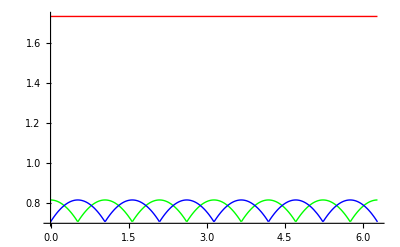

```mathematica
Plot[{Piecewise[{{0, θ≥2 π||θ<0}, {√3, True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Cos[θ], (5 π)/6≤θ≤(7 π)/6}, {√(2/3) Cos[θ], (θ≥0&&6 θ≤π)||(11 π)/6≤θ<2 π}, {-Cos[θ]/(√6)-Sin[θ]/(√2), (7 π)/6<θ≤(3 π)/2}, {Cos[θ]/(√6)-Sin[θ]/(√2), (3 π)/2<θ<(11 π)/6}, {-Cos[θ]/(√6)+Sin[θ]/(√2), π/2≤θ<(5 π)/6}, {Cos[θ]/(√6)+Sin[θ]/(√2), True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Sin[θ], (4 π)/3≤θ≤(5 π)/3}, {√(2/3) Sin[θ], π/3≤θ≤(2 π)/3}, {-Cos[θ]/(√2)+Sin[θ]/(√6), (2 π)/3<θ≤π}, {Cos[θ]/(√2)+Sin[θ]/(√6), θ≥0&&3 θ<π}, {-Cos[θ]/(√2)-Sin[θ]/(√6), π<θ<(4 π)/3}, {Cos[θ]/(√2)-Sin[θ]/(√6), True}}]},{θ,0,2Pi},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

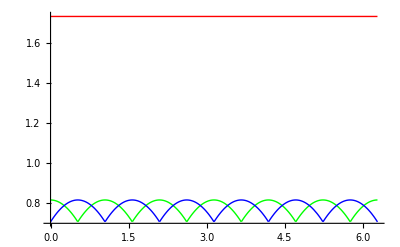

```mathematica
Plot[{√3,   √(2/3) Sin[Mod[θ-Pi/6,Pi/3]+Pi/3],√(2/3) Sin[Mod[θ,Pi/3]+Pi/3]},{θ,0,2Pi},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

```mathematica
Plot[Evaluate[{δYABExtrema[θ,StandardForm,1],δYABExtrema[θ,StandardForm,2],δYABExtrema[θ,StandardForm,3]}],{θ,0,2Pi},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

-Graphics-

```mathematica
d[src_,srcRange_]:=IntegerPart[src*srcRange]/srcRange
```

```mathematica
Manipulate[{MatrixForm[N[d[YAB[θ],tRange].RGBCube]],MatrixForm[N[YAB[θ].RGBCube]]},{{θ,-0.1537},-Pi,Pi},{tRange,1,765,1}]
```

```mathematica
Manipulate[cube=d[d[nYAB[θ],tRange].RGBCube- nYAB[θ].RGBCube,dstRange];{MatrixForm[cube  dstRange],Max[cube] dstRange,Min[cube] dstRange},{{θ,-0.1537},-Pi,Pi},{{tRange,255},1,1024,1},{{dstRange,255},1,255,1}]
```

```mathematica
Union[Flatten[YAB[θ]]]
```

{1/(√3),√(2/3) Cos[θ],-√(2/3) Sin[θ],-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6),Cos[θ]/(√2)+Sin[θ]/(√6)}

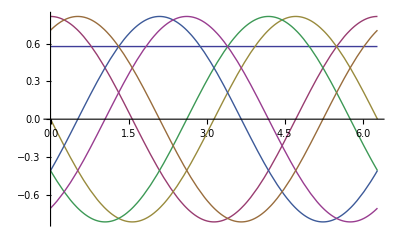

```mathematica
Plot[{1/(√3),√(2/3) Cos[θ],-√(2/3) Sin[θ],-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6),Cos[θ]/(√2)+Sin[θ]/(√6)},{θ,0,2Pi}]
```

```mathematica
TrigReduce[-Cos[θ]/(√6)-Sin[θ]/(√2)]
MatrixForm[TrigFactor[YAB[θ]]]
```

1/6 (-√6 Cos[θ]-3 √2 Sin[θ])

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ])

```mathematica
MatrixForm[TrigFactor[YAB[θ]]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ])

```mathematica
Reduce[TrigReduce[({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}})==YAB[θ]]]
Solve[%,θ]
```

Sin[π/6-θ]==-√3 Sin[θ]+Sin[π/6+θ]&&Cos[π/6+θ]==-2 Sin[θ]+√3 Sin[π/6+θ]&&Cos[θ]==-√3 Sin[θ]+2 Sin[π/6+θ]&&Cos[π/6-θ]==-Sin[θ]+√3 Sin[π/6+θ]

{{}}

```mathematica
Manipulate[{({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[θ+π/6], √(2/3) Cos[θ], √(2/3) Sin[θ-π/6]}, {-√(2/3) Cos[θ+π/6], -√(2/3) Sin[θ], √(2/3) Cos[θ-π/6]}})==YAB[θ],Plot[{-Sin[θ+π/6]/Sin[θ],Cos[θ],Sin[θ-π/6]/Sin[θ]},{θ,0,2Pi}]},{{θ,-0.1537},-Pi,Pi}]
```

```mathematica
TrigReduce[TrigExpand[Sin[θ+π/6]/Sin[θ]]]
TrigReduce[TrigExpand[Sin[θ-π/6]/Sin[θ]]]
```

1/2 (√3+Cot[θ])

1/2 (√3-Cot[θ])

```mathematica
MatrixForm[Series[({{1, 1, 1}, {- Sin[θ+π/6], Cos[θ], Sin[θ-π/6]}, {- Cos[θ+π/6], - Sin[θ], Cos[θ-π/6]}}),{θ,0,6}]]
```

(1 | 1 | 1
-1/2-(√3 θ)/2+θ^2/4+θ^3/(4 √3)-θ^4/48-θ^5/(80 √3)+θ^6/1440+O[θ]^7 | 1-θ^2/2+θ^4/24-θ^6/720+O[θ]^7 | -1/2+(√3 θ)/2+θ^2/4-θ^3/(4 √3)-θ^4/48+θ^5/(80 √3)+θ^6/1440+O[θ]^7
-(√3)/2+θ/2+(√3 θ^2)/4-θ^3/12-θ^4/(16 √3)+θ^5/240+θ^6/(480 √3)+O[θ]^7 | -θ+θ^3/6-θ^5/120+O[θ]^7 | (√3)/2+θ/2-(√3 θ^2)/4-θ^3/12+θ^4/(16 √3)+θ^5/240-θ^6/(480 √3)+O[θ]^7)

```mathematica
rYAB[θ_]:= ({{1, 1, 1}, {- Sin[θ+π/6], Cos[θ], Sin[θ-π/6]}, {- Cos[θ+π/6], - Sin[θ], Cos[θ-π/6]}})
```

```mathematica
Manipulate[cube=d[d[rYAB[θ],tRange].RGBCube- rYAB[θ].RGBCube,dstRange];{MatrixForm[cube  dstRange],Max[cube] dstRange,Min[cube] dstRange},{{θ,-0.1537},-Pi,Pi},{{tRange,255},1,1024,1},{{dstRange,255},1,255,1}]
```

Where does this error ocure

```mathematica
δYABsign[θ_]:=Evaluate[MapThread[Piecewise[{{1,#1},{-1,#2}},0]&,{maskPos[θ],maskNeg[θ],YAB[θ]},2]]
MatrixForm[δYABsign[θ]]
```

MapThread::mptd: Object maskPos[θ] at position {2, 1} in MapThread[TagBox[GridBox[{{"{", GridBox[{{"1", "#1"}, {-1, "#2"}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]] &, {maskPos[θ], maskNeg[θ], {{1/√3, 1/√3, 1/√3}, {-√2/3\ Sin[Times[« 2 »] + θ], √2/3\ Cos[θ], -√2/3\ Sin[Times[« 2 »] + Times[« 2 »]]}, {-√2/3\ Cos[Times[« 2 »] + θ], -√2/3\ Sin[θ], √2/3\ Cos[Times[« 2 »] + Times[« 2 »]]}}}, 2] has only 0 of required 2 dimensions.

MapThread[Piecewise[{{1, #1}, {-1, #2}, {0, True}}]&,{maskPos[θ],maskNeg[θ],{{1/(√3),1/(√3),1/(√3)},{-√(2/3) Sin[π/6+θ],√(2/3) Cos[θ],-√(2/3) Sin[π/6-θ]},{-√(2/3) Cos[π/6+θ],-√(2/3) Sin[θ],√(2/3) Cos[π/6-θ]}}},2]

```mathematica
s=δYABsign[θ].{1,1,1};
```

```mathematica
MatrixForm[PiecewiseExpand[{s[[1]] δYABsign[θ][[1]],s[[2]] δYABsign[θ][[2]],s[[2]] δYABsign[θ][[2]]}]]
```

Piecewise[{{{{0,0,0},{0,0,0},{0,0,0}}, θ≥2 π||θ<0}, {{{3,3,3},{-1,1,1},{-1,1,1}}, π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {{{3,3,3},{0,0,0},{0,0,0}}, θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {{{3,3,3},{1,-1,1},{1,-1,1}}, 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {{{3,3,3},{1,1,-1},{1,1,-1}}, True}}]

```mathematica
Piecewise[{{MatrixForm[{{1,1,1},{0,0,0},{0,0,0}}], θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {MatrixForm[{{1,1,1},{-1,1,1},{-1,1,1}}], π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {MatrixForm[{{1,1,1},{0,0,0},{0,0,0}}], θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {MatrixForm[{{1,1,1},{1,-1,1},{1,-1,1}}], 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {MatrixForm[{{1,1,1},{1,1,-1},{1,1,-1}}], π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}}]
```

Piecewise[{{(1 | 1 | 1
0 | 0 | 0
0 | 0 | 0), θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {(1 | 1 | 1
-1 | 1 | 1
-1 | 1 | 1), π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {(1 | 1 | 1
0 | 0 | 0
0 | 0 | 0), θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {(1 | 1 | 1
1 | -1 | 1
1 | -1 | 1), 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {(1 | 1 | 1
1 | 1 | -1
1 | 1 | -1), π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}, {0, True}}]

```mathematica
Piecewise[{{G+B<1,π/6<θ<π/2||(7 π)/6<θ<(3 π)/2},
{R+G<1,π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6},
{R+B<1,0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π},{False,2 π<θ<0}},Null]
```

Piecewise[{{B+G<1, π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {G+R<1, π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}, {B+R<1, 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {Null, True}}]

```mathematica
{π/6,π/2 ,(7 π)/6,(3 π)/2},
{π/2,(5π)/6 ,(3π)/2,(11π)/6},
{π/6,π/2,(7 π)/6,(3 π)/2}
```

```mathematica
errorFree[pt_,θ_]:=Piecewise[{{pt[[2]]+pt[[3]]<1,π/6<θ<π/2||(7 π)/6<θ<(3 π)/2},
{pt[[1]]+pt[[2]]<1,π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6},
{pt[[1]]+pt[[3]]<1,0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π},{False,2 π<θ<0}},Null]
```

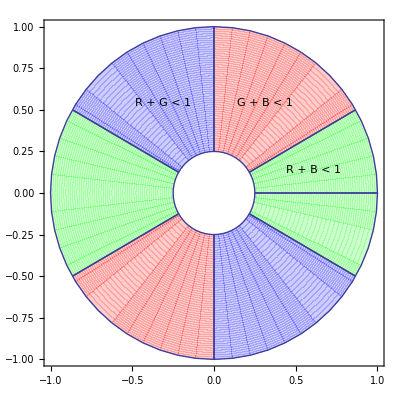

```mathematica
Show[ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1/4,1},RegionFunction->Function[{x,y,θ,r},π/6<θ<π/2||(7 π)/6<θ<(3 π)/2],Mesh->None, PlotStyle->{Red},PlotRange-> 1,PlotLegends->Placed["G + B < 1",{0.3Cos[π/3]+0.5,0.3 Sin[π/3]+0.5}],Axes->False],
ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1/4,1},RegionFunction->Function[{x,y,θ,r},π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6],Mesh->None, PlotStyle->{Blue},PlotRange-> 1,PlotLegends->Placed["R + G < 1",{0.3 Cos[(2 π)/3]+0.5,0.3 Sin[(2 π)/3]+0.5}],Axes->False],
ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1/4,1},RegionFunction->Function[{x,y,θ,r},0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π],Mesh->None, PlotStyle->{Green},PlotRange-> 1,PlotLegends->Placed["R + B < 1",{0.3 Cos[π/14]+0.5,0.3 Sin[π/14]+0.5}],Axes->False]]
```

```mathematica
FullSimplify[YAB[θ].{R,G,B}]
TrigReduce[%]
```

{(B+G+R)/(√3),-((B-2 G+R) Cos[θ])/(√6)+((B-R) Sin[θ])/(√2),((B-R) Cos[θ])/(√2)+((B-2 G+R) Sin[θ])/(√6)}

{(B+G+R)/(√3),1/6 (-√6 B Cos[θ]+2 √6 G Cos[θ]-√6 R Cos[θ]+3 √2 B Sin[θ]-3 √2 R Sin[θ]),1/6 (3 √2 B Cos[θ]-3 √2 R Cos[θ]+√6 B Sin[θ]-2 √6 G Sin[θ]+√6 R Sin[θ])}

```mathematica
FullSimplify[YAB[θ].{R,G,1-R}]
FullSimplify[YAB[θ].{R,G,1-G}]
FullSimplify[YAB[θ].{R,1-R,B}]
```

{(1+G)/(√3),((-1+2 G) Cos[θ])/(√6)+((1-2 R) Sin[θ])/(√2),((3-6 R) Cos[θ]+√3 (1-2 G) Sin[θ])/(3 √2)}

{(1+R)/(√3),((-1+3 G-R) Cos[θ])/(√6)-((-1+G+R) Sin[θ])/(√2),(-3 (-1+G+R) Cos[θ]+√3 (1-3 G+R) Sin[θ])/(3 √2)}

{(1+B)/(√3),-((-2+B+3 R) Cos[θ])/(√6)+((B-R) Sin[θ])/(√2),((B-R) Cos[θ])/(√2)+((-2+B+3 R) Sin[θ])/(√6)}

Apply the limits in Lxy to RGB. We have upper and lower limits on the values for Lxy. To Convert to RGB without stepping outside the cube.

```mathematica
iYAB[θ_]:=Inverse[YAB[θ]]
inYAB[θ_]:=Inverse[nYAB[θ]]
```

```mathematica
RGBPixel[L_,x_,y_,θ_]:=  TrigFactor[inYAB[θ].{L,x,y}]
```

```mathematica
Clear[RGBPixel ,θ]
```

```mathematica
MatrixForm[FullSimplify[TrigFactor[TrigExpand[RGBPixel[L,x,y,θ]]]]]
```

(1/3 (3 L-y Cos[θ-Mod[θ,π/3]]-2 y Cos[θ+Mod[θ,π/3]]-x Cos[Mod[π/6+θ,π/3]] (√3 Cos[θ]+3 Sin[θ])+√3 y Sin[θ-Mod[θ,π/3]]-x (Cos[θ]+√3 Sin[θ]) Sin[Mod[π/6+θ,π/3]])
1/3 (3 L-2 y Sin[θ] (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])+2 x Cos[θ] (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]))
1/3 (3 L+x Cos[Mod[π/6+θ,π/3]] (-√3 Cos[θ]+3 Sin[θ])+y (2 Cos[θ-Mod[θ,π/3]]+Cos[θ+Mod[θ,π/3]]+√3 Sin[θ+Mod[θ,π/3]])+x (-Cos[θ]+√3 Sin[θ]) Sin[Mod[π/6+θ,π/3]]))

```mathematica
Manipulate[Show[{ParametricPlot3D[{RGBPixel[L,a,-maxB,θ],RGBPixel[L,a,maxB,θ]},{L,0,1},{a,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},maxL<L<1-maxL &&-maxA< a <maxA  ],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None],ParametricPlot3D[{RGBPixel[L,-maxA,b,θ],RGBPixel[L,maxA,b,θ]},{L,0,1},{b,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},maxL<L<1-maxL &&-maxB< b <maxB  ],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None],ParametricPlot3D[{RGBPixel[maxL,a,b,θ],RGBPixel[1-maxL,a,b,θ]},{a,-0.5,0.5},{b,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},-maxA< a <maxA &&-maxB< b <maxB],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None]}],{θ,0,2 Pi},{maxL,0,1},{maxA,0,0.5},{maxB,0,0.5}]
```

```mathematica
RGBPixel[minL,maxA,-maxB,θ]
```

{0.23041,-0.753113,1.7227}

```mathematica
minL=0.2;
maxA=0.8;
maxB=0.8;
θ = 0.1;
ParametricPlot3D[{RGBPixel[L,a,-maxB,θ],RGBPixel[L,a,maxB,θ]},{L,0,1},{a,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},minL<L<1-minL &&-maxA< a <maxA  ],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None]
```

-Graphics3D-

```mathematica
Chromatic Bins
```

```mathematica
MatrixForm[√6 YAB[0]]
```

(√2 | √2 | √2
-1 | 2 | -1
-√3 | 0 | √3)

```mathematica
ToMatlab[({{√3, 0, 0}, {0, √6, 0}, {0, 0, √2}}).YAB[0]]
```

[1,1,1;(-1),2,(-1);(-1),0,1];

```mathematica
Simplify[YABAxisRanges[0]]
```

{{0,√3},{-√(2/3),√(2/3)},{-1/(√2),1/(√2)}}

```mathematica
Simplify[2 √(2/3)]
```

2 √(2/3)

```mathematica
N[256 {2 √(2/3),√2}]
```

{418.046,362.039}

```mathematica
N[256 {4,2}]/N[256 {2 √(2/3),√2}]
```

{2.44949,1.41421}

## 2 D rotation Matrix

```mathematica
RotationMatrix2D[θ_]:=1/(√2 Sin[π/4+Mod[θ,Pi/2]] ){{ Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
```

```mathematica
RotationMatrix2DScale[θ_]:=(√2 Sin[π/4+Mod[θ,Pi/2]] )
RotationMatrix2D[θ_]:={{ Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
```

```mathematica
MatrixForm[TrigFactor[RotationMatrix2D[θ]]]
```

((-1/2-ⅈ/2) (-1)^(3/4) Cos[θ] Csc[π/4+Mod[θ,π/2]] | (-1/2-ⅈ/2) (-1)^(3/4) Csc[π/4+Mod[θ,π/2]] Sin[θ]
(1/2+ⅈ/2) (-1)^(3/4) Csc[π/4+Mod[θ,π/2]] Sin[θ] | (-1/2-ⅈ/2) (-1)^(3/4) Cos[θ] Csc[π/4+Mod[θ,π/2]])

```mathematica
minMax2D = RotationMatrix2D[θ].{{-1,-1,1,1},{-1,1,-1,1}};
```

```mathematica
minMax2D
```

{{-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2)},{-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2)}}

```mathematica
Union[minMax2D[[1]]]
```

{-Cos[θ]-Sin[θ],Cos[θ]-Sin[θ],-Cos[θ]+Sin[θ],Cos[θ]+Sin[θ]}

```mathematica
InputForm[RotationMatrixX[θ].RGBCube]
```

{{0, 1, 1, 0, 0, 0, 1, 1}, {0, 0, Cos[θ], Cos[θ], Cos[θ] + Sin[θ], Sin[θ], Sin[θ], Cos[θ] + Sin[θ]}, 
 {0, 0, -Sin[θ], -Sin[θ], Cos[θ] - Sin[θ], Cos[θ], Cos[θ], Cos[θ] - Sin[θ]}}

```mathematica
TrigFactor[Union[minMax2D[[1]]]]
TrigFactor[Union[minMax2D[[2]]]]
```

{(1+ⅈ) (-1)^(3/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1+ⅈ) (-1)^(3/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]]}

{(1+ⅈ) (-1)^(3/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1+ⅈ) (-1)^(3/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]]}

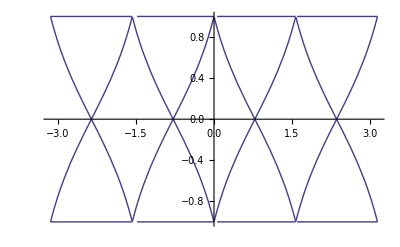

```mathematica
Plot[TrigFactor[Union[minMax2D[[1]]]],{θ,-Pi, Pi}]
```

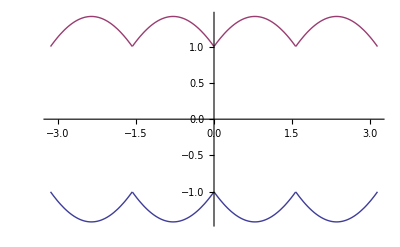

```mathematica
Plot[{-√2 Sin[π/4+Mod[θ,Pi/2]],√2 Sin[π/4+Mod[θ,Pi/2]]},{θ,-Pi, Pi}]
```

```mathematica
RotationMatrixX[θ]
```

{{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}}

```mathematica
square = {{-0.5,0.5,0.5,-0.5},{-0.5,-0.5,0.5,0.5}};
squareShift[θ_]:= {{0.5 Cos[θ],0.5 Cos[θ],0.5 Cos[θ],0.5 Cos[θ]},{0.5 Sin[-θ],0.5 Sin[-θ],0.5 Sin[-θ],0.5 Sin[-θ]}};
```

```mathematica
xyCube[θ_]:=FullSimplify[ Transpose[RotationMatrix2DScale[θ]RotationMatrix2D[θ].square +{{0.5,0.5,0.5,0.5},{0.5,0.5,0.5,0.5}} ]]
```

```mathematica
Manipulate[{θ,Sin[θ]^2,Graphics[{Blue,Polygon[xyCube[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5}]]]]],Black,Rectangle[{0,0},{1,1}]},PlotRange->{{-0.5,1.5},{-0.5 ,1.5}}]},{{θ,0},-Pi/2,Pi/2}]
```

```mathematica
YABAxisRanges[0]
```

{{0,√3},{-(√(3/2))/2-1/(2 √6),(√(3/2))/2+1/(2 √6)},{-1/(√2),1/(√2)}}

```mathematica
RotationMatrix2DScale
```

```mathematica
nYABPolygon[0]
```

{{-1/4,-1/2},{1/4,-1/2},{1/2,0},{1/4,1/2},{-1/4,1/2},{-1/2,0}}

```mathematica
RGBCube
```

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
xyCube[Pi/2]
```

{{0,1,0,1},{0,0,-1,-1}}

```mathematica
FullSimplify[y/Cos[θ] + (1-x-y Tan[θ])Sin[θ]]
```

y Cos[θ]+Sin[θ]-x Sin[θ]

```mathematica
FullSimplify[x/Cos[θ] + (y-x Tan[θ])Sin[θ]]
```

x Cos[θ]+y Sin[θ]

```mathematica
RotationMatrix2D[θ] . {x,y} + {0,Sin[θ]}
```

{x Cos[θ]+y Sin[θ],y Cos[θ]+Sin[θ]-x Sin[θ]}

```mathematica
theta = -0.4823;
c = {0.3329,0.4249};
RotationMatrix2D[theta] . c + {0,Sin[theta]}
```

{0.09785,0.0670188}

```mathematica
RotationMatrix2D[theta]
```

{{0.88593,-0.463818},{0.463818,0.88593}}

```mathematica
RotationMatrix2D[theta] . {0.3329,0.4249} + {0,Sin[theta]}
```

{0.09785,0.0670188}

## Partitioning elipse

```mathematica
surfEllipse=Function[{pt,λ,μ}, (pt[[2]]-μ[[2]])^2/λ[[2]]^2+(pt[[3]]-μ[[3]])^2/λ[[3]]^2<=1 && pt[[1]] = 1]
```

```mathematica
solidEllipse=Function[{pt,λ,μ}, (pt[[2]]-μ[[2]])^2/λ[[2]]^2+(pt[[3]]-μ[[3]])^2/λ[[3]]^2<=1 && pt[[1]] <= 1]
solidCube=Function[{pt}, 0<=pt[[1]] <= 1&& -0.5<=pt[[2]] <= 0.5 && -0.5<=pt[[3]] <= 0.5]
```

Function[{pt,λ,μ},(pt⟦2⟧-μ⟦2⟧)^2/λ⟦2⟧^2+(pt⟦3⟧-μ⟦3⟧)^2/λ⟦3⟧^2≤1&&pt⟦1⟧≤1]

Function[{pt},0≤pt⟦1⟧≤1&&-0.5≤pt⟦2⟧≤0.5&&-0.5≤pt⟦3⟧≤0.5]

```mathematica
Function[{x,y,{a,b}},x^2/a^2+y^2/b^2<1]
```

```mathematica
ellipse[{l,x,y},{2,3},{1,1}]
```

1/4 (-1+l)^2+1/9 (-1+x)^2≤1&&y≤√3

```mathematica
RegionPlot3D[solidCube[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],-0.2,1.2},{Subscript[uT, 2],-0.7,0.7},{Subscript[uT, 3],-0.7,0.7}]
```

-Graphics3D-

```mathematica
RegionPlot3D[ellipse[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.2,0.3},{0,0.1,0.1}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],-0.5,0.5},{Subscript[uT, 3],-0.5,0.5}]
```

-Graphics3D-

```mathematica
iEllipse[pt_,λ_,μ_,θ_]:= Module[{yabPt},yabpt = nYAB[θ].pt; ellipse[yabpt,λ,μ]]
```

```mathematica
iEllipse[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},{Subscript[Λ, 1],Subscript[Λ, 2],Subscript[Λ, 3]},{Subscript[μ, 1],Subscript[μ, 2],Subscript[μ, 3]},θ]
errorFree[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},θ]
```

(((-Cos[θ]-√3 Sin[θ]) uSrc_1)/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]))+(Cos[θ] uSrc_2)/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])+((-Cos[θ]+√3 Sin[θ]) uSrc_3)/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]))-μ_2)^2/Λ_2^2+(((-√3 Cos[θ]+Sin[θ]) uSrc_1)/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]))-(Sin[θ] uSrc_2)/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])+((√3 Cos[θ]+Sin[θ]) uSrc_3)/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]))-μ_3)^2/Λ_3^2≤1&&uSrc_1/3+uSrc_2/3+uSrc_3/3≤1

Piecewise[{{uSrc_2+uSrc_3<1, π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {uSrc_1+uSrc_2<1, π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}, {uSrc_1+uSrc_3<1, 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {Null, True}}]

```mathematica
RegionPlot3D[iEllipse[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.1,0.05},{0,0,0},0],{Subscript[uT, 1],0,1},{Subscript[uT, 2],0,1},{Subscript[uT, 3],0,1}]
```

-Graphics3D-

```mathematica
Manipulate[Show[RegionPlot3D[errorFree[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},θ],{Subscript[uSrc, 1],0,1},{Subscript[uSrc, 2],0,1},{Subscript[uSrc, 3],0,1},PlotStyle->Directive[Green,Opacity[0.5]],Mesh->None],RegionPlot3D[Not[errorFree[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},θ]],{Subscript[uSrc, 1],0,1},{Subscript[uSrc, 2],0,1},{Subscript[uSrc, 3],0,1},PlotStyle->Directive[Red,Opacity[0.5]],Mesh->None],RegionPlot3D[iEllipse[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},{0,0.1,0.05},{0,0,0},θ],{Subscript[uSrc, 1],0,1},{Subscript[uSrc, 2],0,1},{Subscript[uSrc, 3],0,1},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None]],{{θ,0},0,2Pi}]
```

```mathematica
θ=0;
Show[RegionPlot3D[errorFree[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},θ],{Subscript[uSrc, 1],0,1},{Subscript[uSrc, 2],0,1},{Subscript[uSrc, 3],0,1},PlotStyle->Directive[Green,Opacity[0.5]],Mesh->None],RegionPlot3D[Not[errorFree[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},θ]],{Subscript[uSrc, 1],0,1},{Subscript[uSrc, 2],0,1},{Subscript[uSrc, 3],0,1},PlotStyle->Directive[Red,Opacity[0.5]],Mesh->None],RegionPlot3D[iEllipse[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},{0,0.1,0.05},{0,0,0},θ],{Subscript[uSrc, 1],0,1},{Subscript[uSrc, 2],0,1},{Subscript[uSrc, 3],0,1},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None]]
```

-Graphics3D-

```mathematica
nYAB[0].RGBCube
inYAB[0].%
```

{{0,1/3,2/3,1/3,2/3,1/3,2/3,1},{0,-1/4,1/4,1/2,1/4,-1/4,-1/2,0},{0,-1/2,-1/2,0,1/2,1/2,0,0}}

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
inYAB[0]
```

{{1,-2/3,-1},{1,4/3,0},{1,-2/3,1}}

```mathematica
Definition[cube]
```

cube=Function[{pt},0≤pt⟦1⟧≤1&&-0.5≤pt⟦2⟧≤0.5&&-0.5≤pt⟦3⟧≤0.5]

```mathematica
inYAB[0].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}
```

{uT_1-(2 uT_2)/3-uT_3,uT_1+(4 uT_2)/3,uT_1-(2 uT_2)/3+uT_3}

```mathematica
cube[inYAB[0].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}]
```

0≤uT_1-(2 uT_2)/3-uT_3≤1&&-0.5≤uT_1+(4 uT_2)/3≤0.5&&-0.5≤uT_1-(2 uT_2)/3+uT_3≤0.5

```mathematica
Reduce[0≤Subscript[uT, 1]-(2 Subscript[uT, 2])/3-Subscript[uT, 3]≤1&&-0.5≤Subscript[uT, 1]+(4 Subscript[uT, 2])/3≤0.5&&-0.5≤Subscript[uT, 1]-(2 Subscript[uT, 2])/3+Subscript[uT, 3]≤0.5]
```

(-0.333333≤uT_1≤0&&((0.125 (-3.-6. uT_1)≤uT_2<0.125 (3.+12. uT_1)&&0.166667 (-3.-6. uT_1+4. uT_2)≤uT_3≤0.333333 (3. uT_1-2. uT_2))||(uT_2==0.125 (3.+12. uT_1)&&uT_3==0.166667 (-3.-6. uT_1+4. uT_2))))||(0<uT_1<0.333333&&((0.125 (-3.-6. uT_1)≤uT_2<0.125 (-3.+12. uT_1)&&0.333333 (-3.+3. uT_1-2. uT_2)≤uT_3≤0.166667 (3.-6. uT_1+4. uT_2))||(uT_2==0.125 (-3.+12. uT_1)&&0.166667 (-3.-6. uT_1+4. uT_2)≤uT_3≤0.166667 (3.-6. uT_1+4. uT_2))||(0.125 (-3.+12. uT_1)<uT_2≤0.125 (3.-6. uT_1)&&0.166667 (-3.-6. uT_1+4. uT_2)≤uT_3≤0.333333 (3. uT_1-2. uT_2))))||(uT_1==0.333333&&((uT_2==-0.625&&uT_3==-0.25)||(-0.625<uT_2<0.125&&0.333333 (-2.-2. uT_2)≤uT_3≤0.166667 (1.+4. uT_2))||(uT_2==0.125&&-0.75≤uT_3≤0.25)))||(0.333333<uT_1≤0.666667&&((uT_2==0.125 (-9.+12. uT_1)&&uT_3==0.166667 (3.-6. uT_1+4. uT_2))||(0.125 (-9.+12. uT_1)<uT_2≤0.125 (3.-6. uT_1)&&0.333333 (-3.+3. uT_1-2. uT_2)≤uT_3≤0.166667 (3.-6. uT_1+4. uT_2))))

```mathematica
RegionPlot3D[solidCube[nYAB[0].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],0,1},{Subscript[uT, 3],0,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[cube[Inverse[nYAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],0,1},{Subscript[uT, 3],0,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[cube[Inverse[nYAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],-1,1},{Subscript[uT, 2],-1,1},{Subscript[uT, 3],-1,1},Mesh->2,MeshFunctions->Automatic]
```

RegionPlot3D[cube[Inverse[nYAB[0]].{uT_1,uT_2,uT_3}],{uT_1,-1,1},{uT_2,-1,1},{uT_3,-1,1},Mesh→2,MeshFunctions→Automatic]

```mathematica
RegionPlot3D[cube[Inverse[nYAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],-1,1},{Subscript[uT, 2],-1,1},{Subscript[uT, 3],-1,1},Mesh->1,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
ellipse[Transpose[YAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.2,0.3},{0,0.1,0.1}]
```

25. (-0.1+uT_1/(√3)+√(2/3) uT_2)^2+11.1111 (-0.1+uT_1/(√3)-uT_2/(√6)+uT_3/(√2))^2≤1&&uT_1/(√3)-uT_2/(√6)-uT_3/(√2)≤√3

```mathematica
Transpose[YAB[0]].{√3,0,0}
```

{1,1,1}

```mathematica
Clear[θ]
```

```mathematica
YAB[θ].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}
```

{uT_1/(√3)+uT_2/(√3)+uT_3/(√3),-√(2/3) Sin[π/6+θ] uT_1+√(2/3) Cos[θ] uT_2-√(2/3) Sin[π/6-θ] uT_3,-√(2/3) Cos[π/6+θ] uT_1-√(2/3) Sin[θ] uT_2+√(2/3) Cos[π/6-θ] uT_3}

## Gaining an extra integer

```mathematica
MatrixForm[rYAB[θ]]
```

(1 | 1 | 1
-Sin[π/6+θ] | Cos[θ] | -Sin[π/6-θ]
-Cos[π/6+θ] | -Sin[θ] | Cos[π/6-θ])

We have three ranges for θ

π/6<θ<π/2||(7 π)/6<θ<(3 π)/2

```mathematica
MatrixForm[Sign[rYAB[(3 π)/12]]]
MatrixForm[rYAB[(15 π)/12]]
```

(1 | 1 | 1
-1 | 1 | 1
-1 | -1 | 1)

(1 | 1 | 1
(1+√3)/(2 √2) | -1/(√2) | -(-1+√3)/(2 √2)
(-1+√3)/(2 √2) | 1/(√2) | -(1+√3)/(2 √2))

π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6

0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π

```mathematica
errorFree[{Subscript[uSrc, 1],Subscript[uSrc, 2],Subscript[uSrc, 3]},θ]
```

Piecewise[{{uSrc_2+uSrc_3<1, π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {uSrc_1+uSrc_2<1, π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}, {uSrc_1+uSrc_3<1, 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {Null, True}}]